```mathematica
syms5=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols];
```

```mathematica
syms5Null=Sort[Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}],CompareSymbols];
```

```mathematica
Coeff5[k_]:=Table[Coefficient[allGraphs5[k,"colofour"],t],{t,syms5}]
```

```mathematica
Coeff5Null[k_]:=Table[Coefficient[allGraphs5[k,"colofourrealnull"],t],{t,syms5Null}]
```

```mathematica
rn=Monitor[Table[allGraphs5[k,"colofournullvector"]=Coeff5Null[k],{k,Keys[allGraphs5]}],k];
```

```mathematica
r=Monitor[Table[allGraphs5[k,"colofourvector"]=Coeff5[k],{k,Keys[allGraphs5]}],k];
```

```mathematica
CompKey5[k1_,k2_]:=CompareSymbols[SetsToSymbol2[allGraphs5[k1,"vertexsets"]],SetsToSymbol2[allGraphs5[k2,"vertexsets"]]]
```

```mathematica
MyFormula[sets_]:=Product[Style[BellB[n],Red],{n,Map[Length,sets]}]
```

## And now how many times an atom got used

```mathematica
TableForm[Monitor[Table[
With[
{used=Total[
With[
{atom=allGraphs5[k,"colofourrealnull"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofourrealnull"]],atom],1,0],
{m,allGraphs5AtomKeys}]
]],
used2=Total[
With[
{atom=allGraphs5[k,"colofourrealnull"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofourrealnull"]],atom],1,0],
{m,Keys[allGraphs5]}]
]],
ortho=Total[
Table[
If[allGraphs5[k,"colofournullvector"].allGraphs5[m,"colofournullvector"]==0,1,0],
{m,allGraphs5AtomKeys}]],
used5=Sort[Tally[ Table[SymbolToLabel[SetsToSymbol[allGraphs5[j,"vertexsets"]]],
{j,With[
{atom=allGraphs5[k,"colofourrealnull"]},
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofourrealnull"]],atom]&]
]}]]]},

{

 SymbolToLabel[allGraphs5[k,"colofourrealnull"]],MyFormula[allGraphs5[k,"vertexsets"]], used, ortho,Framed[Column[used5]]
}
]

,{k,Sort[allGraphs5NullAtomKeys,CompKey5]}],{k,m}],
TableHeadings->{{},{"partition","formula", "used by null", "ortho null",  "ortho all"}},TableDepth->5]
```

| partition | formula | used by null | ortho null | ortho all
 | 1♁2♁3♁4♁5 | 1^5 | 1 | 51 | {1♁2♁3♁4♁5,1024}
 | 1♁2♁3♁45 | 1^3 2 | 2 | 50 | {1♁2♁3♁45,64}
{1♁2♁3♁4♁5,512}
 | 1♁2♁34♁5 | 1^3 2 | 2 | 50 | {1♁2♁34♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁2♁35♁4 | 1^3 2 | 2 | 50 | {1♁2♁35♁4,64}
{1♁2♁3♁4♁5,512}
 | 1♁23♁4♁5 | 1^3 2 | 2 | 50 | {1♁23♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁24♁3♁5 | 1^3 2 | 2 | 50 | {1♁24♁3♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁25♁3♁4 | 1^3 2 | 2 | 50 | {1♁25♁3♁4,64}
{1♁2♁3♁4♁5,512}
 | 12♁3♁4♁5 | 1^3 2 | 2 | 50 | {12♁3♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 13♁2♁4♁5 | 1^3 2 | 2 | 50 | {13♁2♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 14♁2♁3♁5 | 1^3 2 | 2 | 50 | {14♁2♁3♁5,64}
{1♁2♁3♁4♁5,512}
 | 15♁2♁3♁4 | 1^3 2 | 2 | 50 | {15♁2♁3♁4,64}
{1♁2♁3♁4♁5,512}
 | 1♁23♁45 | 1 2^2 | 4 | 48 | {1♁23♁45,8}
{1♁2♁3♁45,32}
{1♁23♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 1♁24♁35 | 1 2^2 | 4 | 48 | {1♁24♁35,8}
{1♁2♁35♁4,32}
{1♁24♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 1♁25♁34 | 1 2^2 | 4 | 48 | {1♁25♁34,8}
{1♁2♁34♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 12♁3♁45 | 1 2^2 | 4 | 48 | {12♁3♁45,8}
{1♁2♁3♁45,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 12♁34♁5 | 1 2^2 | 4 | 48 | {12♁34♁5,8}
{1♁2♁34♁5,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 12♁35♁4 | 1 2^2 | 4 | 48 | {12♁35♁4,8}
{1♁2♁35♁4,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁2♁45 | 1 2^2 | 4 | 48 | {13♁2♁45,8}
{1♁2♁3♁45,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁24♁5 | 1 2^2 | 4 | 48 | {13♁24♁5,8}
{1♁24♁3♁5,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁25♁4 | 1 2^2 | 4 | 48 | {13♁25♁4,8}
{1♁25♁3♁4,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁2♁35 | 1 2^2 | 4 | 48 | {14♁2♁35,8}
{1♁2♁35♁4,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁23♁5 | 1 2^2 | 4 | 48 | {14♁23♁5,8}
{1♁23♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁25♁3 | 1 2^2 | 4 | 48 | {14♁25♁3,8}
{1♁25♁3♁4,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 15♁2♁34 | 1 2^2 | 4 | 48 | {15♁2♁34,8}
{1♁2♁34♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 15♁23♁4 | 1 2^2 | 4 | 48 | {15♁23♁4,8}
{1♁23♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 15♁24♁3 | 1 2^2 | 4 | 48 | {15♁24♁3,8}
{1♁24♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 1♁2♁345 | 1^2 5 | 5 | 47 | {1♁2♁345,8}
{1♁2♁3♁45,32}
{1♁2♁34♁5,32}
{1♁2♁35♁4,32}
{1♁2♁3♁4♁5,512}
 | 1♁234♁5 | 1^2 5 | 5 | 47 | {1♁234♁5,8}
{1♁2♁34♁5,32}
{1♁23♁4♁5,32}
{1♁24♁3♁5,32}
{1♁2♁3♁4♁5,512}
 | 1♁235♁4 | 1^2 5 | 5 | 47 | {1♁235♁4,8}
{1♁2♁35♁4,32}
{1♁23♁4♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,512}
 | 1♁245♁3 | 1^2 5 | 5 | 47 | {1♁245♁3,8}
{1♁2♁3♁45,32}
{1♁24♁3♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,512}
 | 123♁4♁5 | 1^2 5 | 5 | 47 | {123♁4♁5,8}
{1♁23♁4♁5,32}
{12♁3♁4♁5,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,512}
 | 124♁3♁5 | 1^2 5 | 5 | 47 | {124♁3♁5,8}
{1♁24♁3♁5,32}
{12♁3♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,512}
 | 125♁3♁4 | 1^2 5 | 5 | 47 | {125♁3♁4,8}
{1♁25♁3♁4,32}
{12♁3♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,512}
 | 134♁2♁5 | 1^2 5 | 5 | 47 | {134♁2♁5,8}
{1♁2♁34♁5,32}
{13♁2♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,512}
 | 135♁2♁4 | 1^2 5 | 5 | 47 | {135♁2♁4,8}
{1♁2♁35♁4,32}
{13♁2♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,512}
 | 145♁2♁3 | 1^2 5 | 5 | 47 | {145♁2♁3,8}
{1♁2♁3♁45,32}
{14♁2♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,512}
 | 12♁345 | 2 5 | 10 | 42 | {12♁345,2}
{1♁2♁345,4}
{12♁3♁45,4}
{12♁34♁5,4}
{12♁35♁4,4}
{1♁2♁3♁45,16}
{1♁2♁34♁5,16}
{1♁2♁35♁4,16}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 123♁45 | 2 5 | 10 | 42 | {123♁45,2}
{1♁23♁45,4}
{12♁3♁45,4}
{123♁4♁5,4}
{13♁2♁45,4}
{1♁2♁3♁45,32}
{1♁23♁4♁5,16}
{12♁3♁4♁5,16}
{13♁2♁4♁5,16}
{1♁2♁3♁4♁5,256}
 | 124♁35 | 2 5 | 10 | 42 | {124♁35,2}
{1♁24♁35,4}
{12♁35♁4,4}
{124♁3♁5,4}
{14♁2♁35,4}
{1♁2♁35♁4,32}
{1♁24♁3♁5,16}
{12♁3♁4♁5,16}
{14♁2♁3♁5,16}
{1♁2♁3♁4♁5,256}
 | 125♁34 | 2 5 | 10 | 42 | {125♁34,2}
{1♁25♁34,4}
{12♁34♁5,4}
{125♁3♁4,4}
{15♁2♁34,4}
{1♁2♁34♁5,32}
{1♁25♁3♁4,16}
{12♁3♁4♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,256}
 | 13♁245 | 2 5 | 10 | 42 | {13♁245,2}
{1♁245♁3,4}
{13♁2♁45,4}
{13♁24♁5,4}
{13♁25♁4,4}
{1♁2♁3♁45,16}
{1♁24♁3♁5,16}
{1♁25♁3♁4,16}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 134♁25 | 2 5 | 10 | 42 | {134♁25,2}
{1♁25♁34,4}
{13♁25♁4,4}
{134♁2♁5,4}
{14♁25♁3,4}
{1♁2♁34♁5,16}
{1♁25♁3♁4,32}
{13♁2♁4♁5,16}
{14♁2♁3♁5,16}
{1♁2♁3♁4♁5,256}
 | 135♁24 | 2 5 | 10 | 42 | {135♁24,2}
{1♁24♁35,4}
{13♁24♁5,4}
{135♁2♁4,4}
{15♁24♁3,4}
{1♁2♁35♁4,16}
{1♁24♁3♁5,32}
{13♁2♁4♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,256}
 | 14♁235 | 2 5 | 10 | 42 | {14♁235,2}
{1♁235♁4,4}
{14♁2♁35,4}
{14♁23♁5,4}
{14♁25♁3,4}
{1♁2♁35♁4,16}
{1♁23♁4♁5,16}
{1♁25♁3♁4,16}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 145♁23 | 2 5 | 10 | 42 | {145♁23,2}
{1♁23♁45,4}
{14♁23♁5,4}
{145♁2♁3,4}
{15♁23♁4,4}
{1♁2♁3♁45,16}
{1♁23♁4♁5,32}
{14♁2♁3♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,256}
 | 15♁234 | 2 5 | 10 | 42 | {15♁234,2}
{1♁234♁5,4}
{15♁2♁34,4}
{15♁23♁4,4}
{15♁24♁3,4}
{1♁2♁34♁5,16}
{1♁23♁4♁5,16}
{1♁24♁3♁5,16}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 1♁2345 | 1 15 | 15 | 37 | {1♁2345,2}
{1♁2♁345,4}
{1♁23♁45,4}
{1♁234♁5,4}
{1♁235♁4,4}
{1♁24♁35,4}
{1♁245♁3,4}
{1♁25♁34,4}
{1♁2♁3♁45,32}
{1♁2♁34♁5,32}
{1♁2♁35♁4,32}
{1♁23♁4♁5,32}
{1♁24♁3♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,608}
 | 1234♁5 | 1 15 | 15 | 37 | {1234♁5,2}
{1♁234♁5,4}
{12♁34♁5,4}
{123♁4♁5,4}
{124♁3♁5,4}
{13♁24♁5,4}
{134♁2♁5,4}
{14♁23♁5,4}
{1♁2♁34♁5,32}
{1♁23♁4♁5,32}
{1♁24♁3♁5,32}
{12♁3♁4♁5,32}
{13♁2♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,608}
 | 1235♁4 | 1 15 | 15 | 37 | {1235♁4,2}
{1♁235♁4,4}
{12♁35♁4,4}
{123♁4♁5,4}
{125♁3♁4,4}
{13♁25♁4,4}
{135♁2♁4,4}
{15♁23♁4,4}
{1♁2♁35♁4,32}
{1♁23♁4♁5,32}
{1♁25♁3♁4,32}
{12♁3♁4♁5,32}
{13♁2♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,608}
 | 1245♁3 | 1 15 | 15 | 37 | {1245♁3,2}
{1♁245♁3,4}
{12♁3♁45,4}
{124♁3♁5,4}
{125♁3♁4,4}
{14♁25♁3,4}
{145♁2♁3,4}
{15♁24♁3,4}
{1♁2♁3♁45,32}
{1♁24♁3♁5,32}
{1♁25♁3♁4,32}
{12♁3♁4♁5,32}
{14♁2♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,608}
 | 1345♁2 | 1 15 | 15 | 37 | {1345♁2,2}
{1♁2♁345,4}
{13♁2♁45,4}
{134♁2♁5,4}
{135♁2♁4,4}
{14♁2♁35,4}
{145♁2♁3,4}
{15♁2♁34,4}
{1♁2♁3♁45,32}
{1♁2♁34♁5,32}
{1♁2♁35♁4,32}
{13♁2♁4♁5,32}
{14♁2♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,608}
 | 12345 | 52 | 52 | 0 | {12345,1}
{1♁2345,1}
{12♁345,1}
{123♁45,1}
{1234♁5,1}
{1235♁4,1}
{124♁35,1}
{1245♁3,1}
{125♁34,1}
{13♁245,1}
{134♁25,1}
{1345♁2,1}
{135♁24,1}
{14♁235,1}
{145♁23,1}
{15♁234,1}
{1♁2♁345,4}
{1♁23♁45,4}
{1♁234♁5,4}
{1♁235♁4,4}
{1♁24♁35,4}
{1♁245♁3,4}
{1♁25♁34,4}
{12♁3♁45,4}
{12♁34♁5,4}
{12♁35♁4,4}
{123♁4♁5,4}
{124♁3♁5,4}
{125♁3♁4,4}
{13♁2♁45,4}
{13♁24♁5,4}
{13♁25♁4,4}
{134♁2♁5,4}
{135♁2♁4,4}
{14♁2♁35,4}
{14♁23♁5,4}
{14♁25♁3,4}
{145♁2♁3,4}
{15♁2♁34,4}
{15♁23♁4,4}
{15♁24♁3,4}
{1♁2♁3♁45,38}
{1♁2♁34♁5,38}
{1♁2♁35♁4,38}
{1♁23♁4♁5,38}
{1♁24♁3♁5,38}
{1♁25♁3♁4,38}
{12♁3♁4♁5,38}
{13♁2♁4♁5,38}
{14♁2♁3♁5,38}
{15♁2♁3♁4,38}
{1♁2♁3♁4♁5,728}

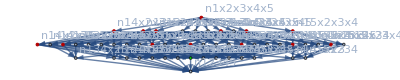

```mathematica
Graph[EdgeList[MobiusGraph4[K5Key, allGraphs5]],
VertexStyle->{n1345x2->Green},
VertexLabels->"Name",  GraphHighlight->Map[Symbol["n"<>StringDrop[SymbolName[#[[1]]],1]]&,{{v134x2x5,4},{v135x2x4,4},{v13x2x45,4},{v13x2x4x5,32},{v145x2x3,4},{v14x2x35,4},{v14x2x3x5,32},{v15x2x34,4},{v15x2x3x4,32},{v1x2x345,4},{v1x2x34x5,32},{v1x2x35x4,32},{v1x2x3x45,32},{v1x2x3x4x5,608}}],
GraphLayout->{"LayeredDigraphEmbedding"}]
```

```mathematica
TableForm[Monitor[Table[
With[
{used=Total[
With[
{atom=allGraphs5[k,"colofourrealnull"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofourrealnull"]],atom],1,0],
{m,allGraphs5AtomKeys}]
]],
used2=Total[
With[
{atom=allGraphs5[k,"colofourrealnull"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofourrealnull"]],atom],1,0],
{m,Keys[allGraphs5]}]
]],
ortho=Total[
Table[
If[allGraphs5[k,"colofournullvector"].allGraphs5[m,"colofournullvector"]==0,1,0],
{m,allGraphs5AtomKeys}]],
used5=Sort[Tally[ Table[SetsToSymbol[allGraphs5[j,"vertexsets"]],
{j,With[
{atom=allGraphs5[k,"colofourrealnull"]},
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofourrealnull"]],atom]&]
]}]]]},

{

 SymbolToLabel[allGraphs5[k,"colofourrealnull"]],MyFormula[allGraphs5[k,"vertexsets"]], used, ortho,Framed[used5]
}
]

,{k,Sort[allGraphs5NullAtomKeys,CompKey5]}],{k,m}],
TableHeadings->{{},{"partition","formula", "used by null", "ortho null",  "ortho all"}},TableDepth->5]
```

| partition | formula | used by null | ortho null | ortho all
 | 1♁2♁3♁4♁5 | 1^5 | 1 | 51 | {{v1x2x3x4x5,1024}}
 | 1♁2♁3♁45 | 1^3 2 | 2 | 50 | {{v1x2x3x45,64},{v1x2x3x4x5,512}}
 | 1♁2♁34♁5 | 1^3 2 | 2 | 50 | {{v1x2x34x5,64},{v1x2x3x4x5,512}}
 | 1♁2♁35♁4 | 1^3 2 | 2 | 50 | {{v1x2x35x4,64},{v1x2x3x4x5,512}}
 | 1♁23♁4♁5 | 1^3 2 | 2 | 50 | {{v1x23x4x5,64},{v1x2x3x4x5,512}}
 | 1♁24♁3♁5 | 1^3 2 | 2 | 50 | {{v1x24x3x5,64},{v1x2x3x4x5,512}}
 | 1♁25♁3♁4 | 1^3 2 | 2 | 50 | {{v1x25x3x4,64},{v1x2x3x4x5,512}}
 | 12♁3♁4♁5 | 1^3 2 | 2 | 50 | {{v12x3x4x5,64},{v1x2x3x4x5,512}}
 | 13♁2♁4♁5 | 1^3 2 | 2 | 50 | {{v13x2x4x5,64},{v1x2x3x4x5,512}}
 | 14♁2♁3♁5 | 1^3 2 | 2 | 50 | {{v14x2x3x5,64},{v1x2x3x4x5,512}}
 | 15♁2♁3♁4 | 1^3 2 | 2 | 50 | {{v15x2x3x4,64},{v1x2x3x4x5,512}}
 | 1♁23♁45 | 1 2^2 | 4 | 48 | {{v1x23x45,8},{v1x23x4x5,32},{v1x2x3x45,32},{v1x2x3x4x5,256}}
 | 1♁24♁35 | 1 2^2 | 4 | 48 | {{v1x24x35,8},{v1x24x3x5,32},{v1x2x35x4,32},{v1x2x3x4x5,256}}
 | 1♁25♁34 | 1 2^2 | 4 | 48 | {{v1x25x34,8},{v1x25x3x4,32},{v1x2x34x5,32},{v1x2x3x4x5,256}}
 | 12♁3♁45 | 1 2^2 | 4 | 48 | {{v12x3x45,8},{v12x3x4x5,32},{v1x2x3x45,32},{v1x2x3x4x5,256}}
 | 12♁34♁5 | 1 2^2 | 4 | 48 | {{v12x34x5,8},{v12x3x4x5,32},{v1x2x34x5,32},{v1x2x3x4x5,256}}
 | 12♁35♁4 | 1 2^2 | 4 | 48 | {{v12x35x4,8},{v12x3x4x5,32},{v1x2x35x4,32},{v1x2x3x4x5,256}}
 | 13♁2♁45 | 1 2^2 | 4 | 48 | {{v13x2x45,8},{v13x2x4x5,32},{v1x2x3x45,32},{v1x2x3x4x5,256}}
 | 13♁24♁5 | 1 2^2 | 4 | 48 | {{v13x24x5,8},{v13x2x4x5,32},{v1x24x3x5,32},{v1x2x3x4x5,256}}
 | 13♁25♁4 | 1 2^2 | 4 | 48 | {{v13x25x4,8},{v13x2x4x5,32},{v1x25x3x4,32},{v1x2x3x4x5,256}}
 | 14♁2♁35 | 1 2^2 | 4 | 48 | {{v14x2x35,8},{v14x2x3x5,32},{v1x2x35x4,32},{v1x2x3x4x5,256}}
 | 14♁23♁5 | 1 2^2 | 4 | 48 | {{v14x23x5,8},{v14x2x3x5,32},{v1x23x4x5,32},{v1x2x3x4x5,256}}
 | 14♁25♁3 | 1 2^2 | 4 | 48 | {{v14x25x3,8},{v14x2x3x5,32},{v1x25x3x4,32},{v1x2x3x4x5,256}}
 | 15♁2♁34 | 1 2^2 | 4 | 48 | {{v15x2x34,8},{v15x2x3x4,32},{v1x2x34x5,32},{v1x2x3x4x5,256}}
 | 15♁23♁4 | 1 2^2 | 4 | 48 | {{v15x23x4,8},{v15x2x3x4,32},{v1x23x4x5,32},{v1x2x3x4x5,256}}
 | 15♁24♁3 | 1 2^2 | 4 | 48 | {{v15x24x3,8},{v15x2x3x4,32},{v1x24x3x5,32},{v1x2x3x4x5,256}}
 | 1♁2♁345 | 1^2 5 | 5 | 47 | {{v1x2x345,8},{v1x2x34x5,32},{v1x2x35x4,32},{v1x2x3x45,32},{v1x2x3x4x5,512}}
 | 1♁234♁5 | 1^2 5 | 5 | 47 | {{v1x234x5,8},{v1x23x4x5,32},{v1x24x3x5,32},{v1x2x34x5,32},{v1x2x3x4x5,512}}
 | 1♁235♁4 | 1^2 5 | 5 | 47 | {{v1x235x4,8},{v1x23x4x5,32},{v1x25x3x4,32},{v1x2x35x4,32},{v1x2x3x4x5,512}}
 | 1♁245♁3 | 1^2 5 | 5 | 47 | {{v1x245x3,8},{v1x24x3x5,32},{v1x25x3x4,32},{v1x2x3x45,32},{v1x2x3x4x5,512}}
 | 123♁4♁5 | 1^2 5 | 5 | 47 | {{v123x4x5,8},{v12x3x4x5,32},{v13x2x4x5,32},{v1x23x4x5,32},{v1x2x3x4x5,512}}
 | 124♁3♁5 | 1^2 5 | 5 | 47 | {{v124x3x5,8},{v12x3x4x5,32},{v14x2x3x5,32},{v1x24x3x5,32},{v1x2x3x4x5,512}}
 | 125♁3♁4 | 1^2 5 | 5 | 47 | {{v125x3x4,8},{v12x3x4x5,32},{v15x2x3x4,32},{v1x25x3x4,32},{v1x2x3x4x5,512}}
 | 134♁2♁5 | 1^2 5 | 5 | 47 | {{v134x2x5,8},{v13x2x4x5,32},{v14x2x3x5,32},{v1x2x34x5,32},{v1x2x3x4x5,512}}
 | 135♁2♁4 | 1^2 5 | 5 | 47 | {{v135x2x4,8},{v13x2x4x5,32},{v15x2x3x4,32},{v1x2x35x4,32},{v1x2x3x4x5,512}}
 | 145♁2♁3 | 1^2 5 | 5 | 47 | {{v145x2x3,8},{v14x2x3x5,32},{v15x2x3x4,32},{v1x2x3x45,32},{v1x2x3x4x5,512}}
 | 12♁345 | 2 5 | 10 | 42 | {{v12x345,2},{v12x34x5,4},{v12x35x4,4},{v12x3x45,4},{v12x3x4x5,32},{v1x2x345,4},{v1x2x34x5,16},{v1x2x35x4,16},{v1x2x3x45,16},{v1x2x3x4x5,256}}
 | 123♁45 | 2 5 | 10 | 42 | {{v123x45,2},{v123x4x5,4},{v12x3x45,4},{v12x3x4x5,16},{v13x2x45,4},{v13x2x4x5,16},{v1x23x45,4},{v1x23x4x5,16},{v1x2x3x45,32},{v1x2x3x4x5,256}}
 | 124♁35 | 2 5 | 10 | 42 | {{v124x35,2},{v124x3x5,4},{v12x35x4,4},{v12x3x4x5,16},{v14x2x35,4},{v14x2x3x5,16},{v1x24x35,4},{v1x24x3x5,16},{v1x2x35x4,32},{v1x2x3x4x5,256}}
 | 125♁34 | 2 5 | 10 | 42 | {{v125x34,2},{v125x3x4,4},{v12x34x5,4},{v12x3x4x5,16},{v15x2x34,4},{v15x2x3x4,16},{v1x25x34,4},{v1x25x3x4,16},{v1x2x34x5,32},{v1x2x3x4x5,256}}
 | 13♁245 | 2 5 | 10 | 42 | {{v13x245,2},{v13x24x5,4},{v13x25x4,4},{v13x2x45,4},{v13x2x4x5,32},{v1x245x3,4},{v1x24x3x5,16},{v1x25x3x4,16},{v1x2x3x45,16},{v1x2x3x4x5,256}}
 | 134♁25 | 2 5 | 10 | 42 | {{v134x25,2},{v134x2x5,4},{v13x25x4,4},{v13x2x4x5,16},{v14x25x3,4},{v14x2x3x5,16},{v1x25x34,4},{v1x25x3x4,32},{v1x2x34x5,16},{v1x2x3x4x5,256}}
 | 135♁24 | 2 5 | 10 | 42 | {{v135x24,2},{v135x2x4,4},{v13x24x5,4},{v13x2x4x5,16},{v15x24x3,4},{v15x2x3x4,16},{v1x24x35,4},{v1x24x3x5,32},{v1x2x35x4,16},{v1x2x3x4x5,256}}
 | 14♁235 | 2 5 | 10 | 42 | {{v14x235,2},{v14x23x5,4},{v14x25x3,4},{v14x2x35,4},{v14x2x3x5,32},{v1x235x4,4},{v1x23x4x5,16},{v1x25x3x4,16},{v1x2x35x4,16},{v1x2x3x4x5,256}}
 | 145♁23 | 2 5 | 10 | 42 | {{v145x23,2},{v145x2x3,4},{v14x23x5,4},{v14x2x3x5,16},{v15x23x4,4},{v15x2x3x4,16},{v1x23x45,4},{v1x23x4x5,32},{v1x2x3x45,16},{v1x2x3x4x5,256}}
 | 15♁234 | 2 5 | 10 | 42 | {{v15x234,2},{v15x23x4,4},{v15x24x3,4},{v15x2x34,4},{v15x2x3x4,32},{v1x234x5,4},{v1x23x4x5,16},{v1x24x3x5,16},{v1x2x34x5,16},{v1x2x3x4x5,256}}
 | 1♁2345 | 1 15 | 15 | 37 | {{v1x2345,2},{v1x234x5,4},{v1x235x4,4},{v1x23x45,4},{v1x23x4x5,32},{v1x245x3,4},{v1x24x35,4},{v1x24x3x5,32},{v1x25x34,4},{v1x25x3x4,32},{v1x2x345,4},{v1x2x34x5,32},{v1x2x35x4,32},{v1x2x3x45,32},{v1x2x3x4x5,608}}
 | 1234♁5 | 1 15 | 15 | 37 | {{v1234x5,2},{v123x4x5,4},{v124x3x5,4},{v12x34x5,4},{v12x3x4x5,32},{v134x2x5,4},{v13x24x5,4},{v13x2x4x5,32},{v14x23x5,4},{v14x2x3x5,32},{v1x234x5,4},{v1x23x4x5,32},{v1x24x3x5,32},{v1x2x34x5,32},{v1x2x3x4x5,608}}
 | 1235♁4 | 1 15 | 15 | 37 | {{v1235x4,2},{v123x4x5,4},{v125x3x4,4},{v12x35x4,4},{v12x3x4x5,32},{v135x2x4,4},{v13x25x4,4},{v13x2x4x5,32},{v15x23x4,4},{v15x2x3x4,32},{v1x235x4,4},{v1x23x4x5,32},{v1x25x3x4,32},{v1x2x35x4,32},{v1x2x3x4x5,608}}
 | 1245♁3 | 1 15 | 15 | 37 | {{v1245x3,2},{v124x3x5,4},{v125x3x4,4},{v12x3x45,4},{v12x3x4x5,32},{v145x2x3,4},{v14x25x3,4},{v14x2x3x5,32},{v15x24x3,4},{v15x2x3x4,32},{v1x245x3,4},{v1x24x3x5,32},{v1x25x3x4,32},{v1x2x3x45,32},{v1x2x3x4x5,608}}
 | 1345♁2 | 1 15 | 15 | 37 | {{v1345x2,2},{v134x2x5,4},{v135x2x4,4},{v13x2x45,4},{v13x2x4x5,32},{v145x2x3,4},{v14x2x35,4},{v14x2x3x5,32},{v15x2x34,4},{v15x2x3x4,32},{v1x2x345,4},{v1x2x34x5,32},{v1x2x35x4,32},{v1x2x3x45,32},{v1x2x3x4x5,608}}
 | 12345 | 52 | 52 | 0 | {{v12345,1},{v1234x5,1},{v1235x4,1},{v123x45,1},{v123x4x5,4},{v1245x3,1},{v124x35,1},{v124x3x5,4},{v125x34,1},{v125x3x4,4},{v12x345,1},{v12x34x5,4},{v12x35x4,4},{v12x3x45,4},{v12x3x4x5,38},{v1345x2,1},{v134x25,1},{v134x2x5,4},{v135x24,1},{v135x2x4,4},{v13x245,1},{v13x24x5,4},{v13x25x4,4},{v13x2x45,4},{v13x2x4x5,38},{v145x23,1},{v145x2x3,4},{v14x235,1},{v14x23x5,4},{v14x25x3,4},{v14x2x35,4},{v14x2x3x5,38},{v15x234,1},{v15x23x4,4},{v15x24x3,4},{v15x2x34,4},{v15x2x3x4,38},{v1x2345,1},{v1x234x5,4},{v1x235x4,4},{v1x23x45,4},{v1x23x4x5,38},{v1x245x3,4},{v1x24x35,4},{v1x24x3x5,38},{v1x25x34,4},{v1x25x3x4,38},{v1x2x345,4},{v1x2x34x5,38},{v1x2x35x4,38},{v1x2x3x45,38},{v1x2x3x4x5,728}}

```mathematica
Now for full base formula
```

base for formula full Sun 16 Jul 2017 16:46:10GMT+2.

```mathematica
TableForm[Monitor[Table[
With[
{used=Total[
With[
{atom=allGraphs5[k,"colofour"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofour"]],atom],1,0],
{m,allGraphs5NullAtomKeys}]
]],
used2=Total[
With[
{atom=allGraphs5[k,"colofour"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofour"]],atom],1,0],
{m,Keys[allGraphs5]}]
]],
ortho=Total[
Table[
If[allGraphs5[k,"colofourvector"].allGraphs5[m,"colofourvector"]==0,1,0],
{m,allGraphs5NullAtomKeys}]],
used5=Sort[Tally[ Table[SymbolToLabel[SetsToSymbol[allGraphs5[j,"vertexsets"]]],
{j,With[
{atom=allGraphs5[k,"colofour"]},
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],atom]&]
]}]]]},

{

 SymbolToLabel[allGraphs5[k,"colofour"]],MyFormula[allGraphs5[k,"vertexsets"]], used, ortho,Framed[Column[used5]]
}
]

,{k,Sort[allGraphs5AtomKeys,CompKey5]}],{k,m}],
TableHeadings->{{},{"partition","formula", "used by null", "ortho null",  "ortho all"}},TableDepth->5]
```

| partition | formula | used by null | ortho null | ortho all
 | 1♁2♁3♁4♁5 | 1^5 | 1 | 51 | {1♁2♁3♁4♁5,1024}
 | 1♁2♁3♁45 | 1^3 2 | 2 | 50 | {1♁2♁3♁45,64}
{1♁2♁3♁4♁5,512}
 | 1♁2♁34♁5 | 1^3 2 | 2 | 50 | {1♁2♁34♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁2♁35♁4 | 1^3 2 | 2 | 50 | {1♁2♁35♁4,64}
{1♁2♁3♁4♁5,512}
 | 1♁23♁4♁5 | 1^3 2 | 2 | 50 | {1♁23♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁24♁3♁5 | 1^3 2 | 2 | 50 | {1♁24♁3♁5,64}
{1♁2♁3♁4♁5,512}
 | 1♁25♁3♁4 | 1^3 2 | 2 | 50 | {1♁25♁3♁4,64}
{1♁2♁3♁4♁5,512}
 | 12♁3♁4♁5 | 1^3 2 | 2 | 50 | {12♁3♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 13♁2♁4♁5 | 1^3 2 | 2 | 50 | {13♁2♁4♁5,64}
{1♁2♁3♁4♁5,512}
 | 14♁2♁3♁5 | 1^3 2 | 2 | 50 | {14♁2♁3♁5,64}
{1♁2♁3♁4♁5,512}
 | 15♁2♁3♁4 | 1^3 2 | 2 | 50 | {15♁2♁3♁4,64}
{1♁2♁3♁4♁5,512}
 | 1♁23♁45 | 1 2^2 | 4 | 48 | {1♁23♁45,8}
{1♁2♁3♁45,32}
{1♁23♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 1♁24♁35 | 1 2^2 | 4 | 48 | {1♁24♁35,8}
{1♁2♁35♁4,32}
{1♁24♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 1♁25♁34 | 1 2^2 | 4 | 48 | {1♁25♁34,8}
{1♁2♁34♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 12♁3♁45 | 1 2^2 | 4 | 48 | {12♁3♁45,8}
{1♁2♁3♁45,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 12♁34♁5 | 1 2^2 | 4 | 48 | {12♁34♁5,8}
{1♁2♁34♁5,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 12♁35♁4 | 1 2^2 | 4 | 48 | {12♁35♁4,8}
{1♁2♁35♁4,32}
{12♁3♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁2♁45 | 1 2^2 | 4 | 48 | {13♁2♁45,8}
{1♁2♁3♁45,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁24♁5 | 1 2^2 | 4 | 48 | {13♁24♁5,8}
{1♁24♁3♁5,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 13♁25♁4 | 1 2^2 | 4 | 48 | {13♁25♁4,8}
{1♁25♁3♁4,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁2♁35 | 1 2^2 | 4 | 48 | {14♁2♁35,8}
{1♁2♁35♁4,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁23♁5 | 1 2^2 | 4 | 48 | {14♁23♁5,8}
{1♁23♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 14♁25♁3 | 1 2^2 | 4 | 48 | {14♁25♁3,8}
{1♁25♁3♁4,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,256}
 | 15♁2♁34 | 1 2^2 | 4 | 48 | {15♁2♁34,8}
{1♁2♁34♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 15♁23♁4 | 1 2^2 | 4 | 48 | {15♁23♁4,8}
{1♁23♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 15♁24♁3 | 1 2^2 | 4 | 48 | {15♁24♁3,8}
{1♁24♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,256}
 | 1♁2♁345 | 1^2 5 | 5 | 47 | {1♁2♁345,8}
{1♁2♁3♁45,32}
{1♁2♁34♁5,32}
{1♁2♁35♁4,32}
{1♁2♁3♁4♁5,128}
 | 1♁234♁5 | 1^2 5 | 5 | 47 | {1♁234♁5,8}
{1♁2♁34♁5,32}
{1♁23♁4♁5,32}
{1♁24♁3♁5,32}
{1♁2♁3♁4♁5,128}
 | 1♁235♁4 | 1^2 5 | 5 | 47 | {1♁235♁4,8}
{1♁2♁35♁4,32}
{1♁23♁4♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,128}
 | 1♁245♁3 | 1^2 5 | 5 | 47 | {1♁245♁3,8}
{1♁2♁3♁45,32}
{1♁24♁3♁5,32}
{1♁25♁3♁4,32}
{1♁2♁3♁4♁5,128}
 | 123♁4♁5 | 1^2 5 | 5 | 47 | {123♁4♁5,8}
{1♁23♁4♁5,32}
{12♁3♁4♁5,32}
{13♁2♁4♁5,32}
{1♁2♁3♁4♁5,128}
 | 124♁3♁5 | 1^2 5 | 5 | 47 | {124♁3♁5,8}
{1♁24♁3♁5,32}
{12♁3♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,128}
 | 125♁3♁4 | 1^2 5 | 5 | 47 | {125♁3♁4,8}
{1♁25♁3♁4,32}
{12♁3♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,128}
 | 134♁2♁5 | 1^2 5 | 5 | 47 | {134♁2♁5,8}
{1♁2♁34♁5,32}
{13♁2♁4♁5,32}
{14♁2♁3♁5,32}
{1♁2♁3♁4♁5,128}
 | 135♁2♁4 | 1^2 5 | 5 | 47 | {135♁2♁4,8}
{1♁2♁35♁4,32}
{13♁2♁4♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,128}
 | 145♁2♁3 | 1^2 5 | 5 | 47 | {145♁2♁3,8}
{1♁2♁3♁45,32}
{14♁2♁3♁5,32}
{15♁2♁3♁4,32}
{1♁2♁3♁4♁5,128}
 | 12♁345 | 2 5 | 10 | 42 | {12♁345,2}
{1♁2♁345,4}
{12♁3♁45,4}
{12♁34♁5,4}
{12♁35♁4,4}
{1♁2♁3♁45,16}
{1♁2♁34♁5,16}
{1♁2♁35♁4,16}
{12♁3♁4♁5,8}
{1♁2♁3♁4♁5,64}
 | 123♁45 | 2 5 | 10 | 42 | {123♁45,2}
{1♁23♁45,4}
{12♁3♁45,4}
{123♁4♁5,4}
{13♁2♁45,4}
{1♁2♁3♁45,8}
{1♁23♁4♁5,16}
{12♁3♁4♁5,16}
{13♁2♁4♁5,16}
{1♁2♁3♁4♁5,64}
 | 124♁35 | 2 5 | 10 | 42 | {124♁35,2}
{1♁24♁35,4}
{12♁35♁4,4}
{124♁3♁5,4}
{14♁2♁35,4}
{1♁2♁35♁4,8}
{1♁24♁3♁5,16}
{12♁3♁4♁5,16}
{14♁2♁3♁5,16}
{1♁2♁3♁4♁5,64}
 | 125♁34 | 2 5 | 10 | 42 | {125♁34,2}
{1♁25♁34,4}
{12♁34♁5,4}
{125♁3♁4,4}
{15♁2♁34,4}
{1♁2♁34♁5,8}
{1♁25♁3♁4,16}
{12♁3♁4♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,64}
 | 13♁245 | 2 5 | 10 | 42 | {13♁245,2}
{1♁245♁3,4}
{13♁2♁45,4}
{13♁24♁5,4}
{13♁25♁4,4}
{1♁2♁3♁45,16}
{1♁24♁3♁5,16}
{1♁25♁3♁4,16}
{13♁2♁4♁5,8}
{1♁2♁3♁4♁5,64}
 | 134♁25 | 2 5 | 10 | 42 | {134♁25,2}
{1♁25♁34,4}
{13♁25♁4,4}
{134♁2♁5,4}
{14♁25♁3,4}
{1♁2♁34♁5,16}
{1♁25♁3♁4,8}
{13♁2♁4♁5,16}
{14♁2♁3♁5,16}
{1♁2♁3♁4♁5,64}
 | 135♁24 | 2 5 | 10 | 42 | {135♁24,2}
{1♁24♁35,4}
{13♁24♁5,4}
{135♁2♁4,4}
{15♁24♁3,4}
{1♁2♁35♁4,16}
{1♁24♁3♁5,8}
{13♁2♁4♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,64}
 | 14♁235 | 2 5 | 10 | 42 | {14♁235,2}
{1♁235♁4,4}
{14♁2♁35,4}
{14♁23♁5,4}
{14♁25♁3,4}
{1♁2♁35♁4,16}
{1♁23♁4♁5,16}
{1♁25♁3♁4,16}
{14♁2♁3♁5,8}
{1♁2♁3♁4♁5,64}
 | 145♁23 | 2 5 | 10 | 42 | {145♁23,2}
{1♁23♁45,4}
{14♁23♁5,4}
{145♁2♁3,4}
{15♁23♁4,4}
{1♁2♁3♁45,16}
{1♁23♁4♁5,8}
{14♁2♁3♁5,16}
{15♁2♁3♁4,16}
{1♁2♁3♁4♁5,64}
 | 15♁234 | 2 5 | 10 | 42 | {15♁234,2}
{1♁234♁5,4}
{15♁2♁34,4}
{15♁23♁4,4}
{15♁24♁3,4}
{1♁2♁34♁5,16}
{1♁23♁4♁5,16}
{1♁24♁3♁5,16}
{15♁2♁3♁4,8}
{1♁2♁3♁4♁5,64}
 | 1♁2345 | 1 15 | 15 | 37 | {1♁2345,2}
{1♁2♁345,4}
{1♁23♁45,4}
{1♁234♁5,4}
{1♁235♁4,4}
{1♁24♁35,4}
{1♁245♁3,4}
{1♁25♁34,4}
{1♁2♁3♁45,8}
{1♁2♁34♁5,8}
{1♁2♁35♁4,8}
{1♁23♁4♁5,8}
{1♁24♁3♁5,8}
{1♁25♁3♁4,8}
{1♁2♁3♁4♁5,16}
 | 1234♁5 | 1 15 | 15 | 37 | {1234♁5,2}
{1♁234♁5,4}
{12♁34♁5,4}
{123♁4♁5,4}
{124♁3♁5,4}
{13♁24♁5,4}
{134♁2♁5,4}
{14♁23♁5,4}
{1♁2♁34♁5,8}
{1♁23♁4♁5,8}
{1♁24♁3♁5,8}
{12♁3♁4♁5,8}
{13♁2♁4♁5,8}
{14♁2♁3♁5,8}
{1♁2♁3♁4♁5,16}
 | 1235♁4 | 1 15 | 15 | 37 | {1235♁4,2}
{1♁235♁4,4}
{12♁35♁4,4}
{123♁4♁5,4}
{125♁3♁4,4}
{13♁25♁4,4}
{135♁2♁4,4}
{15♁23♁4,4}
{1♁2♁35♁4,8}
{1♁23♁4♁5,8}
{1♁25♁3♁4,8}
{12♁3♁4♁5,8}
{13♁2♁4♁5,8}
{15♁2♁3♁4,8}
{1♁2♁3♁4♁5,16}
 | 1245♁3 | 1 15 | 15 | 37 | {1245♁3,2}
{1♁245♁3,4}
{12♁3♁45,4}
{124♁3♁5,4}
{125♁3♁4,4}
{14♁25♁3,4}
{145♁2♁3,4}
{15♁24♁3,4}
{1♁2♁3♁45,8}
{1♁24♁3♁5,8}
{1♁25♁3♁4,8}
{12♁3♁4♁5,8}
{14♁2♁3♁5,8}
{15♁2♁3♁4,8}
{1♁2♁3♁4♁5,16}
 | 1345♁2 | 1 15 | 15 | 37 | {1345♁2,2}
{1♁2♁345,4}
{13♁2♁45,4}
{134♁2♁5,4}
{135♁2♁4,4}
{14♁2♁35,4}
{145♁2♁3,4}
{15♁2♁34,4}
{1♁2♁3♁45,8}
{1♁2♁34♁5,8}
{1♁2♁35♁4,8}
{13♁2♁4♁5,8}
{14♁2♁3♁5,8}
{15♁2♁3♁4,8}
{1♁2♁3♁4♁5,16}
 | 12345 | 52 | 52 | 0 | {12345,1}
{1♁2345,1}
{12♁345,1}
{123♁45,1}
{1234♁5,1}
{1235♁4,1}
{124♁35,1}
{1245♁3,1}
{125♁34,1}
{13♁245,1}
{134♁25,1}
{1345♁2,1}
{135♁24,1}
{14♁235,1}
{145♁23,1}
{15♁234,1}
{1♁2♁345,1}
{1♁23♁45,1}
{1♁234♁5,1}
{1♁235♁4,1}
{1♁24♁35,1}
{1♁245♁3,1}
{1♁25♁34,1}
{12♁3♁45,1}
{12♁34♁5,1}
{12♁35♁4,1}
{123♁4♁5,1}
{124♁3♁5,1}
{125♁3♁4,1}
{13♁2♁45,1}
{13♁24♁5,1}
{13♁25♁4,1}
{134♁2♁5,1}
{135♁2♁4,1}
{14♁2♁35,1}
{14♁23♁5,1}
{14♁25♁3,1}
{145♁2♁3,1}
{15♁2♁34,1}
{15♁23♁4,1}
{15♁24♁3,1}
{1♁2♁3♁45,1}
{1♁2♁34♁5,1}
{1♁2♁35♁4,1}
{1♁23♁4♁5,1}
{1♁24♁3♁5,1}
{1♁25♁3♁4,1}
{12♁3♁4♁5,1}
{13♁2♁4♁5,1}
{14♁2♁3♁5,1}
{15♁2♁3♁4,1}
{1♁2♁3♁4♁5,1}

```mathematica
TableForm[Monitor[Table[
With[
{used=Total[
With[
{atom=allGraphs5[k,"colofour"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofour"]],atom],1,0],
{m,allGraphs5NullAtomKeys}]
]],
used2=Total[
With[
{atom=allGraphs5[k,"colofour"]},
Table[
If[MemberQ[ListofVars[allGraphs5[m,"colofour"]],atom],1,0],
{m,Keys[allGraphs5]}]
]],
ortho=Total[
Table[
If[allGraphs5[k,"colofourvector"].allGraphs5[m,"colofourvector"]==0,1,0],
{m,allGraphs5NullAtomKeys}]],
used5=Sort[Tally[ Table[SetsToSymbol[allGraphs5[j,"vertexsets"]],
{j,With[
{atom=allGraphs5[k,"colofour"]},
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],atom]&]
]}]]]},

{

 SymbolToLabel[allGraphs5[k,"colofour"]],MyFormula[allGraphs5[k,"vertexsets"]], used, ortho,Framed[used5]
}
]

,{k,Take[Sort[allGraphs5AtomKeys,CompKey5],-3]}],{k,m}],
TableHeadings->{{},{"partition","formula", "used by null", "ortho null",  "ortho all"}},TableDepth->5]
```

| partition | formula | used by null | ortho null | ortho all
 | 1245♁3 | 1 15 | 15 | 37 | {{v1245x3,2},{v124x3x5,4},{v125x3x4,4},{v12x3x45,4},{v12x3x4x5,8},{v145x2x3,4},{v14x25x3,4},{v14x2x3x5,8},{v15x24x3,4},{v15x2x3x4,8},{v1x245x3,4},{v1x24x3x5,8},{v1x25x3x4,8},{v1x2x3x45,8},{v1x2x3x4x5,16}}
 | 1345♁2 | 1 15 | 15 | 37 | {{v1345x2,2},{v134x2x5,4},{v135x2x4,4},{v13x2x45,4},{v13x2x4x5,8},{v145x2x3,4},{v14x2x35,4},{v14x2x3x5,8},{v15x2x34,4},{v15x2x3x4,8},{v1x2x345,4},{v1x2x34x5,8},{v1x2x35x4,8},{v1x2x3x45,8},{v1x2x3x4x5,16}}
 | 12345 | 52 | 52 | 0 | {{v12345,1},{v1234x5,1},{v1235x4,1},{v123x45,1},{v123x4x5,1},{v1245x3,1},{v124x35,1},{v124x3x5,1},{v125x34,1},{v125x3x4,1},{v12x345,1},{v12x34x5,1},{v12x35x4,1},{v12x3x45,1},{v12x3x4x5,1},{v1345x2,1},{v134x25,1},{v134x2x5,1},{v135x24,1},{v135x2x4,1},{v13x245,1},{v13x24x5,1},{v13x25x4,1},{v13x2x45,1},{v13x2x4x5,1},{v145x23,1},{v145x2x3,1},{v14x235,1},{v14x23x5,1},{v14x25x3,1},{v14x2x35,1},{v14x2x3x5,1},{v15x234,1},{v15x23x4,1},{v15x24x3,1},{v15x2x34,1},{v15x2x3x4,1},{v1x2345,1},{v1x234x5,1},{v1x235x4,1},{v1x23x45,1},{v1x23x4x5,1},{v1x245x3,1},{v1x24x35,1},{v1x24x3x5,1},{v1x25x34,1},{v1x25x3x4,1},{v1x2x345,1},{v1x2x34x5,1},{v1x2x35x4,1},{v1x2x3x45,1},{v1x2x3x4x5,1}}

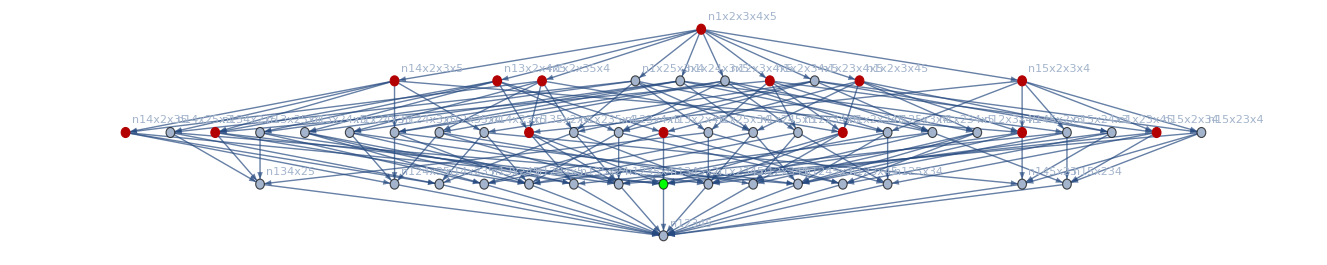

```mathematica
Graph[EdgeList[MobiusGraph4[K5Key, allGraphs5]],
VertexStyle->{n1345x2->Green},
VertexLabels->"Name",  GraphHighlight->Map[Symbol["n"<>StringDrop[SymbolName[#[[1]]],1]]&,{{v134x2x5,4},{v135x2x4,4},{v13x2x45,4},{v13x2x4x5,8},{v145x2x3,4},{v14x2x35,4},{v14x2x3x5,8},{v15x2x34,4},{v15x2x3x4,8},{v1x2x345,4},{v1x2x34x5,8},{v1x2x35x4,8},{v1x2x3x45,8},{v1x2x3x4x5,16}}],
GraphLayout->{"LayeredDigraphEmbedding"}]
```

## Atom to atom five

```mathematica
full=Association[];Table[full[s]=Association[];Table[full[s,t]=0,{t,syms5}],{s,syms5}];
```

```mathematica
HandleFormula[syms_]:=Block[{},
Table[Table[full[s,t]=full[s,t]+1,{t,syms}],{s,syms}]
]
```

```mathematica
Table[HandleFormula[ListofVars[allGraphs5[k,"colofour"]]],{k,Keys[allGraphs5]}];
```

```mathematica
mFull=Map[Values[#]&,Values[full]];
```

```mathematica
SymmetricMatrixQ[mFull]
```

True

```mathematica
MatrixRank[mFull]
```

52

```mathematica
MatrixForm[Map[Values[#]&,Values[full]],TableHeadings->{syms5,Map[Rotate[#,Pi/2]&,syms5]}]
```

( | v1x2x3x4x5 | v1x2x3x45 | v1x2x34x5 | v1x2x35x4 | v1x23x4x5 | v1x24x3x5 | v1x25x3x4 | v12x3x4x5 | v13x2x4x5 | v14x2x3x5 | v15x2x3x4 | v1x23x45 | v1x24x35 | v1x25x34 | v12x3x45 | v12x34x5 | v12x35x4 | v13x2x45 | v13x24x5 | v13x25x4 | v14x2x35 | v14x23x5 | v14x25x3 | v15x2x34 | v15x23x4 | v15x24x3 | v1x2x345 | v1x234x5 | v1x235x4 | v1x245x3 | v123x4x5 | v124x3x5 | v125x3x4 | v134x2x5 | v135x2x4 | v145x2x3 | v12x345 | v123x45 | v124x35 | v125x34 | v13x245 | v134x25 | v135x24 | v14x235 | v145x23 | v15x234 | v1x2345 | v1234x5 | v1235x4 | v1245x3 | v1345x2 | v12345
v1x2x3x4x5 | 1024 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 16 | 16 | 1
v1x2x3x45 | 512 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 288 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 160 | 64 | 64 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 80 | 72 | 32 | 32 | 80 | 32 | 32 | 32 | 80 | 32 | 24 | 8 | 8 | 24 | 24 | 2
v1x2x34x5 | 512 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 64 | 64 | 80 | 32 | 32 | 72 | 32 | 80 | 32 | 32 | 32 | 80 | 24 | 24 | 8 | 8 | 24 | 2
v1x2x35x4 | 512 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 64 | 80 | 32 | 72 | 32 | 32 | 32 | 80 | 80 | 32 | 32 | 24 | 8 | 24 | 8 | 24 | 2
v1x23x4x5 | 512 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 64 | 160 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 64 | 32 | 80 | 32 | 32 | 32 | 32 | 32 | 80 | 72 | 80 | 24 | 24 | 24 | 8 | 8 | 2
v1x24x3x5 | 512 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 64 | 160 | 64 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 32 | 32 | 80 | 32 | 80 | 32 | 72 | 32 | 32 | 80 | 24 | 24 | 8 | 24 | 8 | 2
v1x25x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 64 | 160 | 160 | 64 | 64 | 160 | 64 | 64 | 64 | 32 | 32 | 32 | 80 | 80 | 72 | 32 | 80 | 32 | 32 | 24 | 8 | 24 | 24 | 8 | 2
v12x3x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 160 | 160 | 160 | 64 | 64 | 64 | 72 | 80 | 80 | 80 | 32 | 32 | 32 | 32 | 32 | 32 | 8 | 24 | 24 | 24 | 8 | 2
v13x2x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 160 | 64 | 64 | 160 | 160 | 64 | 32 | 80 | 32 | 32 | 72 | 80 | 80 | 32 | 32 | 32 | 8 | 24 | 24 | 8 | 24 | 2
v14x2x3x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 64 | 160 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 72 | 80 | 32 | 8 | 24 | 8 | 24 | 24 | 2
v15x2x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 64 | 64 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 160 | 32 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 72 | 8 | 8 | 24 | 24 | 24 | 2
v1x23x45 | 256 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 328 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 32 | 32 | 80 | 40 | 92 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 40 | 36 | 12 | 12 | 12 | 12 | 4
v1x24x35 | 256 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 64 | 328 | 64 | 64 | 64 | 144 | 64 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 80 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 40 | 16 | 92 | 16 | 40 | 16 | 92 | 40 | 16 | 40 | 36 | 12 | 12 | 12 | 12 | 4
v1x25x34 | 256 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 64 | 64 | 328 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 144 | 64 | 64 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 32 | 32 | 40 | 16 | 16 | 92 | 40 | 92 | 16 | 40 | 16 | 40 | 36 | 12 | 12 | 12 | 12 | 4
v12x3x45 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 144 | 64 | 64 | 328 | 144 | 144 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 92 | 92 | 40 | 40 | 40 | 16 | 16 | 16 | 40 | 16 | 12 | 12 | 12 | 36 | 12 | 4
v12x34x5 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 64 | 144 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 32 | 92 | 40 | 40 | 92 | 16 | 40 | 16 | 16 | 16 | 40 | 12 | 36 | 12 | 12 | 12 | 4
v12x35x4 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 144 | 64 | 144 | 144 | 328 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 80 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 92 | 40 | 92 | 40 | 16 | 16 | 40 | 40 | 16 | 16 | 12 | 12 | 36 | 12 | 12 | 4
v13x2x45 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 144 | 64 | 64 | 144 | 64 | 64 | 328 | 144 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 32 | 32 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 40 | 92 | 16 | 16 | 92 | 40 | 40 | 16 | 40 | 16 | 12 | 12 | 12 | 12 | 36 | 4
v13x24x5 | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 80 | 32 | 16 | 40 | 40 | 16 | 92 | 40 | 92 | 16 | 16 | 40 | 12 | 36 | 12 | 12 | 12 | 4
v13x25x4 | 256 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 64 | 64 | 144 | 64 | 64 | 64 | 144 | 144 | 328 | 64 | 64 | 144 | 64 | 64 | 64 | 32 | 32 | 80 | 80 | 80 | 32 | 80 | 80 | 80 | 32 | 16 | 40 | 16 | 40 | 92 | 92 | 40 | 40 | 16 | 16 | 12 | 12 | 36 | 12 | 12 | 4
v14x2x35 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 328 | 144 | 144 | 64 | 64 | 64 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 40 | 16 | 92 | 16 | 16 | 40 | 40 | 92 | 40 | 16 | 12 | 12 | 12 | 12 | 36 | 4
v14x23x5 | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 144 | 64 | 32 | 80 | 80 | 32 | 80 | 80 | 32 | 80 | 32 | 80 | 16 | 40 | 40 | 16 | 16 | 40 | 16 | 92 | 92 | 40 | 12 | 36 | 12 | 12 | 12 | 4
v14x25x3 | 256 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 144 | 144 | 328 | 64 | 64 | 64 | 32 | 32 | 80 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 16 | 16 | 40 | 40 | 40 | 92 | 16 | 92 | 40 | 16 | 12 | 12 | 12 | 36 | 12 | 4
v15x2x34 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 64 | 64 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 328 | 144 | 144 | 80 | 80 | 32 | 32 | 32 | 32 | 80 | 80 | 80 | 80 | 40 | 16 | 16 | 92 | 16 | 40 | 40 | 16 | 40 | 92 | 12 | 12 | 12 | 12 | 36 | 4
v15x23x4 | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 144 | 328 | 144 | 32 | 80 | 80 | 32 | 80 | 32 | 80 | 32 | 80 | 80 | 16 | 40 | 16 | 40 | 16 | 16 | 40 | 40 | 92 | 92 | 12 | 12 | 36 | 12 | 12 | 4
v15x24x3 | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 144 | 328 | 32 | 80 | 32 | 80 | 32 | 80 | 80 | 32 | 80 | 80 | 16 | 16 | 40 | 40 | 40 | 16 | 92 | 16 | 40 | 92 | 12 | 12 | 12 | 36 | 12 | 4
v1x2x345 | 128 | 160 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 232 | 48 | 48 | 48 | 16 | 16 | 16 | 48 | 48 | 48 | 116 | 20 | 20 | 20 | 24 | 24 | 24 | 24 | 24 | 24 | 44 | 8 | 8 | 8 | 44 | 5
v1x234x5 | 128 | 64 | 160 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 48 | 232 | 48 | 48 | 48 | 48 | 16 | 48 | 16 | 16 | 24 | 24 | 24 | 20 | 24 | 24 | 20 | 24 | 20 | 116 | 44 | 44 | 8 | 8 | 8 | 5
v1x235x4 | 128 | 64 | 64 | 160 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 80 | 32 | 48 | 48 | 232 | 48 | 48 | 16 | 48 | 16 | 48 | 16 | 24 | 24 | 20 | 24 | 24 | 20 | 24 | 116 | 20 | 24 | 44 | 8 | 44 | 8 | 8 | 5
v1x245x3 | 128 | 160 | 64 | 64 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 48 | 48 | 48 | 232 | 16 | 48 | 48 | 16 | 16 | 48 | 24 | 20 | 24 | 24 | 116 | 20 | 20 | 24 | 24 | 24 | 44 | 8 | 8 | 44 | 8 | 5
v123x4x5 | 128 | 64 | 64 | 64 | 160 | 64 | 64 | 160 | 160 | 64 | 64 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 16 | 48 | 48 | 16 | 232 | 48 | 48 | 48 | 48 | 16 | 20 | 116 | 24 | 24 | 20 | 24 | 24 | 24 | 20 | 24 | 8 | 44 | 44 | 8 | 8 | 5
v124x3x5 | 128 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 64 | 160 | 64 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 16 | 48 | 16 | 48 | 48 | 232 | 48 | 48 | 16 | 48 | 20 | 24 | 116 | 24 | 24 | 24 | 20 | 20 | 24 | 24 | 8 | 44 | 8 | 44 | 8 | 5
v125x3x4 | 128 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 64 | 160 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 16 | 16 | 48 | 48 | 48 | 48 | 232 | 16 | 48 | 48 | 20 | 24 | 24 | 116 | 24 | 20 | 24 | 24 | 24 | 20 | 8 | 8 | 44 | 44 | 8 | 5
v134x2x5 | 128 | 64 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 32 | 32 | 80 | 32 | 80 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 48 | 48 | 16 | 16 | 48 | 48 | 16 | 232 | 48 | 48 | 24 | 24 | 24 | 20 | 20 | 116 | 24 | 20 | 24 | 24 | 8 | 44 | 8 | 8 | 44 | 5
v135x2x4 | 128 | 64 | 64 | 160 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 32 | 80 | 32 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 48 | 16 | 48 | 16 | 48 | 16 | 48 | 48 | 232 | 48 | 24 | 24 | 20 | 24 | 20 | 24 | 116 | 24 | 24 | 20 | 8 | 8 | 44 | 8 | 44 | 5
v145x2x3 | 128 | 160 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 48 | 16 | 16 | 48 | 16 | 48 | 48 | 48 | 48 | 232 | 24 | 20 | 24 | 24 | 24 | 24 | 24 | 20 | 116 | 20 | 8 | 8 | 8 | 44 | 44 | 5
v12x345 | 64 | 80 | 80 | 80 | 32 | 32 | 32 | 72 | 32 | 32 | 32 | 40 | 40 | 40 | 92 | 92 | 92 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 16 | 16 | 116 | 24 | 24 | 24 | 20 | 20 | 20 | 24 | 24 | 24 | 138 | 26 | 26 | 26 | 12 | 12 | 12 | 12 | 12 | 12 | 22 | 12 | 12 | 12 | 22 | 10
v123x45 | 64 | 72 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 32 | 32 | 92 | 16 | 16 | 92 | 40 | 40 | 92 | 40 | 40 | 16 | 40 | 16 | 16 | 40 | 16 | 20 | 24 | 24 | 20 | 116 | 24 | 24 | 24 | 24 | 20 | 26 | 138 | 12 | 12 | 26 | 12 | 12 | 12 | 26 | 12 | 12 | 22 | 22 | 12 | 12 | 10
v124x35 | 64 | 32 | 32 | 72 | 32 | 80 | 32 | 80 | 32 | 80 | 32 | 16 | 92 | 16 | 40 | 40 | 92 | 16 | 40 | 16 | 92 | 40 | 40 | 16 | 16 | 40 | 20 | 24 | 20 | 24 | 24 | 116 | 24 | 24 | 20 | 24 | 26 | 12 | 138 | 12 | 12 | 12 | 26 | 26 | 12 | 12 | 12 | 22 | 12 | 22 | 12 | 10
v125x34 | 64 | 32 | 72 | 32 | 32 | 32 | 80 | 80 | 32 | 32 | 80 | 16 | 16 | 92 | 40 | 92 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 40 | 40 | 20 | 20 | 24 | 24 | 24 | 24 | 116 | 20 | 24 | 24 | 26 | 12 | 12 | 138 | 12 | 26 | 12 | 12 | 12 | 26 | 12 | 12 | 22 | 22 | 12 | 10
v13x245 | 64 | 80 | 32 | 32 | 32 | 80 | 80 | 32 | 72 | 32 | 32 | 40 | 40 | 40 | 40 | 16 | 16 | 92 | 92 | 92 | 16 | 16 | 40 | 16 | 16 | 40 | 24 | 24 | 24 | 116 | 20 | 24 | 24 | 20 | 20 | 24 | 12 | 26 | 12 | 12 | 138 | 26 | 26 | 12 | 12 | 12 | 22 | 12 | 12 | 22 | 12 | 10
v134x25 | 64 | 32 | 80 | 32 | 32 | 32 | 72 | 32 | 80 | 80 | 32 | 16 | 16 | 92 | 16 | 40 | 16 | 40 | 40 | 92 | 40 | 40 | 92 | 40 | 16 | 16 | 24 | 24 | 20 | 20 | 24 | 24 | 20 | 116 | 24 | 24 | 12 | 12 | 12 | 26 | 26 | 138 | 12 | 26 | 12 | 12 | 12 | 22 | 12 | 12 | 22 | 10
v135x24 | 64 | 32 | 32 | 80 | 32 | 72 | 32 | 32 | 80 | 32 | 80 | 16 | 92 | 16 | 16 | 16 | 40 | 40 | 92 | 40 | 40 | 16 | 16 | 40 | 40 | 92 | 24 | 20 | 24 | 20 | 24 | 20 | 24 | 24 | 116 | 24 | 12 | 12 | 26 | 12 | 26 | 12 | 138 | 12 | 12 | 26 | 12 | 12 | 22 | 12 | 22 | 10
v14x235 | 64 | 32 | 32 | 80 | 80 | 32 | 80 | 32 | 32 | 72 | 32 | 40 | 40 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 92 | 92 | 16 | 40 | 16 | 24 | 24 | 116 | 24 | 24 | 20 | 24 | 20 | 24 | 20 | 12 | 12 | 26 | 12 | 12 | 26 | 12 | 138 | 26 | 12 | 22 | 12 | 22 | 12 | 12 | 10
v145x23 | 64 | 80 | 32 | 32 | 72 | 32 | 32 | 32 | 32 | 80 | 80 | 92 | 16 | 16 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 40 | 40 | 92 | 40 | 24 | 20 | 20 | 24 | 20 | 24 | 24 | 24 | 24 | 116 | 12 | 26 | 12 | 12 | 12 | 12 | 12 | 26 | 138 | 26 | 12 | 12 | 12 | 22 | 22 | 10
v15x234 | 64 | 32 | 80 | 32 | 80 | 80 | 32 | 32 | 32 | 32 | 72 | 40 | 40 | 40 | 16 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 16 | 92 | 92 | 92 | 24 | 116 | 24 | 24 | 24 | 24 | 20 | 24 | 20 | 20 | 12 | 12 | 12 | 26 | 12 | 12 | 26 | 12 | 26 | 138 | 22 | 22 | 12 | 12 | 12 | 10
v1x2345 | 16 | 24 | 24 | 24 | 24 | 24 | 24 | 8 | 8 | 8 | 8 | 36 | 36 | 36 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 44 | 44 | 44 | 44 | 8 | 8 | 8 | 8 | 8 | 8 | 22 | 12 | 12 | 12 | 22 | 12 | 12 | 22 | 12 | 22 | 94 | 10 | 10 | 10 | 10 | 15
v1234x5 | 16 | 8 | 24 | 8 | 24 | 24 | 8 | 24 | 24 | 24 | 8 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 8 | 44 | 8 | 8 | 44 | 44 | 8 | 44 | 8 | 8 | 12 | 22 | 22 | 12 | 12 | 22 | 12 | 12 | 12 | 22 | 10 | 94 | 10 | 10 | 10 | 15
v1235x4 | 16 | 8 | 8 | 24 | 24 | 8 | 24 | 24 | 24 | 8 | 24 | 12 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 36 | 12 | 8 | 8 | 44 | 8 | 44 | 8 | 44 | 8 | 44 | 8 | 12 | 22 | 12 | 22 | 12 | 12 | 22 | 22 | 12 | 12 | 10 | 10 | 94 | 10 | 10 | 15
v1245x3 | 16 | 24 | 8 | 8 | 8 | 24 | 24 | 24 | 8 | 24 | 24 | 12 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 8 | 8 | 8 | 44 | 8 | 44 | 44 | 8 | 8 | 44 | 12 | 12 | 22 | 22 | 22 | 12 | 12 | 12 | 22 | 12 | 10 | 10 | 10 | 94 | 10 | 15
v1345x2 | 16 | 24 | 24 | 24 | 8 | 8 | 8 | 8 | 24 | 24 | 24 | 12 | 12 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 44 | 8 | 8 | 8 | 8 | 8 | 8 | 44 | 44 | 44 | 22 | 12 | 12 | 12 | 12 | 22 | 22 | 12 | 22 | 12 | 10 | 10 | 10 | 10 | 94 | 15
v12345 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 15 | 15 | 15 | 15 | 15 | 52)

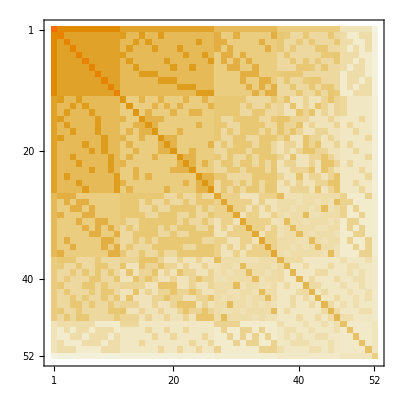

```mathematica
MatrixPlot[Map[Values[#]&,Values[full]]]
```

```mathematica
null=Association[];Table[null[s]=Association[];Table[null[s,t]=0,{t,syms5Null}],{s,syms5Null}];
```

```mathematica
HandleFormulaNull[syms_]:=Block[{},
Table[Table[null[s,t]=null[s,t]+1,{t,syms}],{s,syms}]
]
```

```mathematica
Table[HandleFormulaNull[ListofVars[allGraphs5[k,"colofourrealnull"]]],{k,Keys[allGraphs5]}];
```

```mathematica
MatrixForm[Map[Values[#]&,Values[null]],TableHeadings->{syms5Null,Map[Rotate[#,Pi/2]&,syms5Null]}]
```

( | n1x2x3x4x5 | n1x2x3x45 | n1x2x34x5 | n1x2x35x4 | n1x23x4x5 | n1x24x3x5 | n1x25x3x4 | n12x3x4x5 | n13x2x4x5 | n14x2x3x5 | n15x2x3x4 | n1x23x45 | n1x24x35 | n1x25x34 | n12x3x45 | n12x34x5 | n12x35x4 | n13x2x45 | n13x24x5 | n13x25x4 | n14x2x35 | n14x23x5 | n14x25x3 | n15x2x34 | n15x23x4 | n15x24x3 | n1x2x345 | n1x234x5 | n1x235x4 | n1x245x3 | n123x4x5 | n124x3x5 | n125x3x4 | n134x2x5 | n135x2x4 | n145x2x3 | n12x345 | n123x45 | n124x35 | n125x34 | n13x245 | n134x25 | n135x24 | n14x235 | n145x23 | n15x234 | n1x2345 | n1234x5 | n1235x4 | n1245x3 | n1345x2 | n12345
n1x2x3x4x5 | 1024 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 608 | 608 | 608 | 608 | 608 | 728
n1x2x3x45 | 512 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 288 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 416 | 256 | 256 | 416 | 256 | 256 | 256 | 256 | 256 | 416 | 208 | 288 | 128 | 128 | 208 | 128 | 128 | 128 | 208 | 128 | 416 | 304 | 304 | 416 | 416 | 452
n1x2x34x5 | 512 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 416 | 416 | 256 | 256 | 256 | 256 | 256 | 416 | 256 | 256 | 208 | 128 | 128 | 288 | 128 | 208 | 128 | 128 | 128 | 208 | 416 | 416 | 304 | 304 | 416 | 452
n1x2x35x4 | 512 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 416 | 256 | 416 | 256 | 256 | 256 | 256 | 256 | 416 | 256 | 208 | 128 | 288 | 128 | 128 | 128 | 208 | 208 | 128 | 128 | 416 | 304 | 416 | 304 | 416 | 452
n1x23x4x5 | 512 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 256 | 416 | 416 | 256 | 416 | 256 | 256 | 256 | 256 | 256 | 128 | 208 | 128 | 128 | 128 | 128 | 128 | 208 | 288 | 208 | 416 | 416 | 416 | 304 | 304 | 452
n1x24x3x5 | 512 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 256 | 416 | 256 | 416 | 256 | 416 | 256 | 256 | 256 | 256 | 128 | 128 | 208 | 128 | 208 | 128 | 288 | 128 | 128 | 208 | 416 | 416 | 304 | 416 | 304 | 452
n1x25x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 256 | 256 | 416 | 416 | 256 | 256 | 416 | 256 | 256 | 256 | 128 | 128 | 128 | 208 | 208 | 288 | 128 | 208 | 128 | 128 | 416 | 304 | 416 | 416 | 304 | 452
n12x3x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 416 | 416 | 416 | 256 | 256 | 256 | 288 | 208 | 208 | 208 | 128 | 128 | 128 | 128 | 128 | 128 | 304 | 416 | 416 | 416 | 304 | 452
n13x2x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 416 | 256 | 256 | 416 | 416 | 256 | 128 | 208 | 128 | 128 | 288 | 208 | 208 | 128 | 128 | 128 | 304 | 416 | 416 | 304 | 416 | 452
n14x2x3x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 256 | 416 | 256 | 416 | 256 | 416 | 128 | 128 | 208 | 128 | 128 | 208 | 128 | 288 | 208 | 128 | 304 | 416 | 304 | 416 | 416 | 452
n15x2x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 256 | 256 | 256 | 256 | 256 | 256 | 416 | 256 | 416 | 416 | 128 | 128 | 128 | 208 | 128 | 128 | 208 | 128 | 208 | 288 | 304 | 304 | 416 | 416 | 416 | 452
n1x23x45 | 256 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 328 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 208 | 208 | 208 | 208 | 208 | 128 | 128 | 128 | 128 | 208 | 104 | 236 | 64 | 64 | 104 | 64 | 64 | 104 | 236 | 104 | 292 | 208 | 208 | 208 | 208 | 286
n1x24x35 | 256 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 64 | 328 | 64 | 64 | 64 | 144 | 64 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 208 | 208 | 208 | 208 | 128 | 208 | 128 | 128 | 208 | 128 | 104 | 64 | 236 | 64 | 104 | 64 | 236 | 104 | 64 | 104 | 292 | 208 | 208 | 208 | 208 | 286
n1x25x34 | 256 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 64 | 64 | 328 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 144 | 64 | 64 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 208 | 128 | 128 | 104 | 64 | 64 | 236 | 104 | 236 | 64 | 104 | 64 | 104 | 292 | 208 | 208 | 208 | 208 | 286
n12x3x45 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 144 | 64 | 64 | 328 | 144 | 144 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 236 | 236 | 104 | 104 | 104 | 64 | 64 | 64 | 104 | 64 | 208 | 208 | 208 | 292 | 208 | 286
n12x34x5 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 64 | 144 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 208 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 128 | 128 | 236 | 104 | 104 | 236 | 64 | 104 | 64 | 64 | 64 | 104 | 208 | 292 | 208 | 208 | 208 | 286
n12x35x4 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 144 | 64 | 144 | 144 | 328 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 208 | 128 | 208 | 128 | 208 | 208 | 208 | 128 | 208 | 128 | 236 | 104 | 236 | 104 | 64 | 64 | 104 | 104 | 64 | 64 | 208 | 208 | 292 | 208 | 208 | 286
n13x2x45 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 144 | 64 | 64 | 144 | 64 | 64 | 328 | 144 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 208 | 128 | 128 | 208 | 208 | 128 | 128 | 208 | 208 | 208 | 104 | 236 | 64 | 64 | 236 | 104 | 104 | 64 | 104 | 64 | 208 | 208 | 208 | 208 | 292 | 286
n13x24x5 | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 128 | 208 | 128 | 208 | 208 | 208 | 128 | 208 | 208 | 128 | 64 | 104 | 104 | 64 | 236 | 104 | 236 | 64 | 64 | 104 | 208 | 292 | 208 | 208 | 208 | 286
n13x25x4 | 256 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 64 | 64 | 144 | 64 | 64 | 64 | 144 | 144 | 328 | 64 | 64 | 144 | 64 | 64 | 64 | 128 | 128 | 208 | 208 | 208 | 128 | 208 | 208 | 208 | 128 | 64 | 104 | 64 | 104 | 236 | 236 | 104 | 104 | 64 | 64 | 208 | 208 | 292 | 208 | 208 | 286
n14x2x35 | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 328 | 144 | 144 | 64 | 64 | 64 | 208 | 128 | 208 | 128 | 128 | 208 | 128 | 208 | 208 | 208 | 104 | 64 | 236 | 64 | 64 | 104 | 104 | 236 | 104 | 64 | 208 | 208 | 208 | 208 | 292 | 286
n14x23x5 | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 144 | 64 | 128 | 208 | 208 | 128 | 208 | 208 | 128 | 208 | 128 | 208 | 64 | 104 | 104 | 64 | 64 | 104 | 64 | 236 | 236 | 104 | 208 | 292 | 208 | 208 | 208 | 286
n14x25x3 | 256 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 144 | 144 | 328 | 64 | 64 | 64 | 128 | 128 | 208 | 208 | 128 | 208 | 208 | 208 | 128 | 208 | 64 | 64 | 104 | 104 | 104 | 236 | 64 | 236 | 104 | 64 | 208 | 208 | 208 | 292 | 208 | 286
n15x2x34 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 64 | 64 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 328 | 144 | 144 | 208 | 208 | 128 | 128 | 128 | 128 | 208 | 208 | 208 | 208 | 104 | 64 | 64 | 236 | 64 | 104 | 104 | 64 | 104 | 236 | 208 | 208 | 208 | 208 | 292 | 286
n15x23x4 | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 144 | 328 | 144 | 128 | 208 | 208 | 128 | 208 | 128 | 208 | 128 | 208 | 208 | 64 | 104 | 64 | 104 | 64 | 64 | 104 | 104 | 236 | 236 | 208 | 208 | 292 | 208 | 208 | 286
n15x24x3 | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 144 | 328 | 128 | 208 | 128 | 208 | 128 | 208 | 208 | 128 | 208 | 208 | 64 | 64 | 104 | 104 | 104 | 64 | 236 | 64 | 104 | 236 | 208 | 208 | 208 | 292 | 208 | 286
n1x2x345 | 512 | 416 | 416 | 416 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 128 | 128 | 616 | 336 | 336 | 336 | 256 | 256 | 256 | 336 | 336 | 336 | 308 | 208 | 208 | 208 | 168 | 168 | 168 | 168 | 168 | 168 | 524 | 360 | 360 | 360 | 524 | 524
n1x234x5 | 512 | 256 | 416 | 256 | 416 | 416 | 256 | 256 | 256 | 256 | 256 | 208 | 208 | 208 | 128 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 128 | 208 | 208 | 208 | 336 | 616 | 336 | 336 | 336 | 336 | 256 | 336 | 256 | 256 | 168 | 168 | 168 | 208 | 168 | 168 | 208 | 168 | 208 | 308 | 524 | 524 | 360 | 360 | 360 | 524
n1x235x4 | 512 | 256 | 256 | 416 | 416 | 256 | 416 | 256 | 256 | 256 | 256 | 208 | 208 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 128 | 208 | 128 | 336 | 336 | 616 | 336 | 336 | 256 | 336 | 256 | 336 | 256 | 168 | 168 | 208 | 168 | 168 | 208 | 168 | 308 | 208 | 168 | 524 | 360 | 524 | 360 | 360 | 524
n1x245x3 | 512 | 416 | 256 | 256 | 256 | 416 | 416 | 256 | 256 | 256 | 256 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 208 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 336 | 336 | 336 | 616 | 256 | 336 | 336 | 256 | 256 | 336 | 168 | 208 | 168 | 168 | 308 | 208 | 208 | 168 | 168 | 168 | 524 | 360 | 360 | 524 | 360 | 524
n123x4x5 | 512 | 256 | 256 | 256 | 416 | 256 | 256 | 416 | 416 | 256 | 256 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 208 | 208 | 128 | 208 | 128 | 128 | 208 | 128 | 256 | 336 | 336 | 256 | 616 | 336 | 336 | 336 | 336 | 256 | 208 | 308 | 168 | 168 | 208 | 168 | 168 | 168 | 208 | 168 | 360 | 524 | 524 | 360 | 360 | 524
n124x3x5 | 512 | 256 | 256 | 256 | 256 | 416 | 256 | 416 | 256 | 416 | 256 | 128 | 208 | 128 | 208 | 208 | 208 | 128 | 208 | 128 | 208 | 208 | 208 | 128 | 128 | 208 | 256 | 336 | 256 | 336 | 336 | 616 | 336 | 336 | 256 | 336 | 208 | 168 | 308 | 168 | 168 | 168 | 208 | 208 | 168 | 168 | 360 | 524 | 360 | 524 | 360 | 524
n125x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 416 | 416 | 256 | 256 | 416 | 128 | 128 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 256 | 256 | 336 | 336 | 336 | 336 | 616 | 256 | 336 | 336 | 208 | 168 | 168 | 308 | 168 | 208 | 168 | 168 | 168 | 208 | 360 | 360 | 524 | 524 | 360 | 524
n134x2x5 | 512 | 256 | 416 | 256 | 256 | 256 | 256 | 256 | 416 | 416 | 256 | 128 | 128 | 208 | 128 | 208 | 128 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 128 | 128 | 336 | 336 | 256 | 256 | 336 | 336 | 256 | 616 | 336 | 336 | 168 | 168 | 168 | 208 | 208 | 308 | 168 | 208 | 168 | 168 | 360 | 524 | 360 | 360 | 524 | 524
n135x2x4 | 512 | 256 | 256 | 416 | 256 | 256 | 256 | 256 | 416 | 256 | 416 | 128 | 208 | 128 | 128 | 128 | 208 | 208 | 208 | 208 | 208 | 128 | 128 | 208 | 208 | 208 | 336 | 256 | 336 | 256 | 336 | 256 | 336 | 336 | 616 | 336 | 168 | 168 | 208 | 168 | 208 | 168 | 308 | 168 | 168 | 208 | 360 | 360 | 524 | 360 | 524 | 524
n145x2x3 | 512 | 416 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 416 | 416 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 128 | 128 | 208 | 208 | 208 | 208 | 208 | 208 | 336 | 256 | 256 | 336 | 256 | 336 | 336 | 336 | 336 | 616 | 168 | 208 | 168 | 168 | 168 | 168 | 168 | 208 | 308 | 208 | 360 | 360 | 360 | 524 | 524 | 524
n12x345 | 256 | 208 | 208 | 208 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 104 | 104 | 104 | 236 | 236 | 236 | 104 | 64 | 64 | 104 | 64 | 64 | 104 | 64 | 64 | 308 | 168 | 168 | 168 | 208 | 208 | 208 | 168 | 168 | 168 | 354 | 170 | 170 | 170 | 84 | 84 | 84 | 84 | 84 | 84 | 262 | 250 | 250 | 250 | 262 | 338
n123x45 | 256 | 288 | 128 | 128 | 208 | 128 | 128 | 208 | 208 | 128 | 128 | 236 | 64 | 64 | 236 | 104 | 104 | 236 | 104 | 104 | 64 | 104 | 64 | 64 | 104 | 64 | 208 | 168 | 168 | 208 | 308 | 168 | 168 | 168 | 168 | 208 | 170 | 354 | 84 | 84 | 170 | 84 | 84 | 84 | 170 | 84 | 250 | 262 | 262 | 250 | 250 | 338
n124x35 | 256 | 128 | 128 | 288 | 128 | 208 | 128 | 208 | 128 | 208 | 128 | 64 | 236 | 64 | 104 | 104 | 236 | 64 | 104 | 64 | 236 | 104 | 104 | 64 | 64 | 104 | 208 | 168 | 208 | 168 | 168 | 308 | 168 | 168 | 208 | 168 | 170 | 84 | 354 | 84 | 84 | 84 | 170 | 170 | 84 | 84 | 250 | 262 | 250 | 262 | 250 | 338
n125x34 | 256 | 128 | 288 | 128 | 128 | 128 | 208 | 208 | 128 | 128 | 208 | 64 | 64 | 236 | 104 | 236 | 104 | 64 | 64 | 104 | 64 | 64 | 104 | 236 | 104 | 104 | 208 | 208 | 168 | 168 | 168 | 168 | 308 | 208 | 168 | 168 | 170 | 84 | 84 | 354 | 84 | 170 | 84 | 84 | 84 | 170 | 250 | 250 | 262 | 262 | 250 | 338
n13x245 | 256 | 208 | 128 | 128 | 128 | 208 | 208 | 128 | 288 | 128 | 128 | 104 | 104 | 104 | 104 | 64 | 64 | 236 | 236 | 236 | 64 | 64 | 104 | 64 | 64 | 104 | 168 | 168 | 168 | 308 | 208 | 168 | 168 | 208 | 208 | 168 | 84 | 170 | 84 | 84 | 354 | 170 | 170 | 84 | 84 | 84 | 262 | 250 | 250 | 262 | 250 | 338
n134x25 | 256 | 128 | 208 | 128 | 128 | 128 | 288 | 128 | 208 | 208 | 128 | 64 | 64 | 236 | 64 | 104 | 64 | 104 | 104 | 236 | 104 | 104 | 236 | 104 | 64 | 64 | 168 | 168 | 208 | 208 | 168 | 168 | 208 | 308 | 168 | 168 | 84 | 84 | 84 | 170 | 170 | 354 | 84 | 170 | 84 | 84 | 250 | 262 | 250 | 250 | 262 | 338
n135x24 | 256 | 128 | 128 | 208 | 128 | 288 | 128 | 128 | 208 | 128 | 208 | 64 | 236 | 64 | 64 | 64 | 104 | 104 | 236 | 104 | 104 | 64 | 64 | 104 | 104 | 236 | 168 | 208 | 168 | 208 | 168 | 208 | 168 | 168 | 308 | 168 | 84 | 84 | 170 | 84 | 170 | 84 | 354 | 84 | 84 | 170 | 250 | 250 | 262 | 250 | 262 | 338
n14x235 | 256 | 128 | 128 | 208 | 208 | 128 | 208 | 128 | 128 | 288 | 128 | 104 | 104 | 104 | 64 | 64 | 104 | 64 | 64 | 104 | 236 | 236 | 236 | 64 | 104 | 64 | 168 | 168 | 308 | 168 | 168 | 208 | 168 | 208 | 168 | 208 | 84 | 84 | 170 | 84 | 84 | 170 | 84 | 354 | 170 | 84 | 262 | 250 | 262 | 250 | 250 | 338
n145x23 | 256 | 208 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 208 | 208 | 236 | 64 | 64 | 104 | 64 | 64 | 104 | 64 | 64 | 104 | 236 | 104 | 104 | 236 | 104 | 168 | 208 | 208 | 168 | 208 | 168 | 168 | 168 | 168 | 308 | 84 | 170 | 84 | 84 | 84 | 84 | 84 | 170 | 354 | 170 | 250 | 250 | 250 | 262 | 262 | 338
n15x234 | 256 | 128 | 208 | 128 | 208 | 208 | 128 | 128 | 128 | 128 | 288 | 104 | 104 | 104 | 64 | 104 | 64 | 64 | 104 | 64 | 64 | 104 | 64 | 236 | 236 | 236 | 168 | 308 | 168 | 168 | 168 | 168 | 208 | 168 | 208 | 208 | 84 | 84 | 84 | 170 | 84 | 84 | 170 | 84 | 170 | 354 | 262 | 262 | 250 | 250 | 250 | 338
n1x2345 | 608 | 416 | 416 | 416 | 416 | 416 | 416 | 304 | 304 | 304 | 304 | 292 | 292 | 292 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 524 | 524 | 524 | 524 | 360 | 360 | 360 | 360 | 360 | 360 | 262 | 250 | 250 | 250 | 262 | 250 | 250 | 262 | 250 | 262 | 830 | 510 | 510 | 510 | 510 | 760
n1234x5 | 608 | 304 | 416 | 304 | 416 | 416 | 304 | 416 | 416 | 416 | 304 | 208 | 208 | 208 | 208 | 292 | 208 | 208 | 292 | 208 | 208 | 292 | 208 | 208 | 208 | 208 | 360 | 524 | 360 | 360 | 524 | 524 | 360 | 524 | 360 | 360 | 250 | 262 | 262 | 250 | 250 | 262 | 250 | 250 | 250 | 262 | 510 | 830 | 510 | 510 | 510 | 760
n1235x4 | 608 | 304 | 304 | 416 | 416 | 304 | 416 | 416 | 416 | 304 | 416 | 208 | 208 | 208 | 208 | 208 | 292 | 208 | 208 | 292 | 208 | 208 | 208 | 208 | 292 | 208 | 360 | 360 | 524 | 360 | 524 | 360 | 524 | 360 | 524 | 360 | 250 | 262 | 250 | 262 | 250 | 250 | 262 | 262 | 250 | 250 | 510 | 510 | 830 | 510 | 510 | 760
n1245x3 | 608 | 416 | 304 | 304 | 304 | 416 | 416 | 416 | 304 | 416 | 416 | 208 | 208 | 208 | 292 | 208 | 208 | 208 | 208 | 208 | 208 | 208 | 292 | 208 | 208 | 292 | 360 | 360 | 360 | 524 | 360 | 524 | 524 | 360 | 360 | 524 | 250 | 250 | 262 | 262 | 262 | 250 | 250 | 250 | 262 | 250 | 510 | 510 | 510 | 830 | 510 | 760
n1345x2 | 608 | 416 | 416 | 416 | 304 | 304 | 304 | 304 | 416 | 416 | 416 | 208 | 208 | 208 | 208 | 208 | 208 | 292 | 208 | 208 | 292 | 208 | 208 | 292 | 208 | 208 | 524 | 360 | 360 | 360 | 360 | 360 | 360 | 524 | 524 | 524 | 262 | 250 | 250 | 250 | 250 | 262 | 262 | 250 | 262 | 250 | 510 | 510 | 510 | 510 | 830 | 760
n12345 | 728 | 452 | 452 | 452 | 452 | 452 | 452 | 452 | 452 | 452 | 452 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 286 | 524 | 524 | 524 | 524 | 524 | 524 | 524 | 524 | 524 | 524 | 338 | 338 | 338 | 338 | 338 | 338 | 338 | 338 | 338 | 338 | 760 | 760 | 760 | 760 | 760 | 1224)

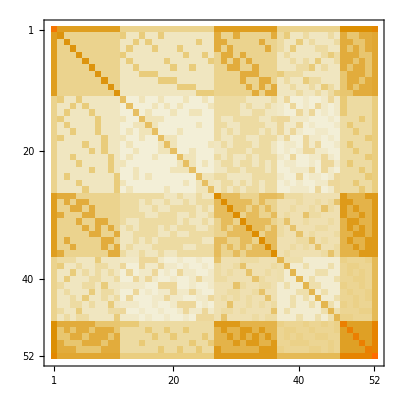

```mathematica
MatrixPlot[Map[Values[#]&,Values[null]]]
```

## Mixed atoms

```mathematica
full2=Association[];Table[full2[s]=Association[];Table[full2[s,t]=0,{t,syms5Null}],{s,syms5}];
```

```mathematica
HandleFormula[syms_,symsNull_]:=Block[{},
Table[Table[full2[s,t]=full2[s,t]+1,{t,symsNull}],{s,syms}]
]
```

```mathematica
Table[HandleFormula[ListofVars[allGraphs5[k,"colofour"]],ListofVars[allGraphs5[k,"colofourrealnull"]]],{k,Keys[allGraphs5]}];
```

```mathematica
mFull2=Map[Values[#]&,Values[full2]];
```

```mathematica
Map[Total,mFull2]
```

{21432,9552,9552,9552,9552,9552,9552,9552,9552,9552,9552,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,4266,2088,2088,2088,2088,2088,2088,2088,2088,2088,2088,936,936,936,936,936,936,936,936,936,936,309,309,309,309,309,52}

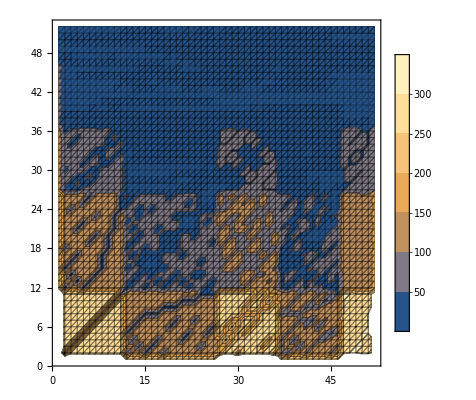

```mathematica
ListContourPlot[Map[Values[#]&,Values[full2]],BoundaryStyle->Directive[Red,Thick],Mesh->All,PlotTheme->"Detailed"]
```

```mathematica
MatrixForm[Map[Values[#]&,Values[full2]],TableHeadings->{syms5Null,Map[Rotate[#,Pi/2]&,syms5]}]
```

( | v1x2x3x4x5 | v1x2x3x45 | v1x2x34x5 | v1x2x35x4 | v1x23x4x5 | v1x24x3x5 | v1x25x3x4 | v12x3x4x5 | v13x2x4x5 | v14x2x3x5 | v15x2x3x4 | v1x23x45 | v1x24x35 | v1x25x34 | v12x3x45 | v12x34x5 | v12x35x4 | v13x2x45 | v13x24x5 | v13x25x4 | v14x2x35 | v14x23x5 | v14x25x3 | v15x2x34 | v15x23x4 | v15x24x3 | v1x2x345 | v1x234x5 | v1x235x4 | v1x245x3 | v123x4x5 | v124x3x5 | v125x3x4 | v134x2x5 | v135x2x4 | v145x2x3 | v12x345 | v123x45 | v124x35 | v125x34 | v13x245 | v134x25 | v135x24 | v14x235 | v145x23 | v15x234 | v1x2345 | v1234x5 | v1235x4 | v1245x3 | v1345x2 | v12345
n1x2x3x4x5 | 1024 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 608 | 608 | 608 | 608 | 608 | 728
n1x2x3x45 | 512 | 64 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 32 | 128 | 128 | 32 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 160 | 256 | 256 | 160 | 256 | 256 | 256 | 256 | 256 | 160 | 80 | 32 | 128 | 128 | 80 | 128 | 128 | 128 | 80 | 128 | 256 | 304 | 304 | 256 | 256 | 352
n1x2x34x5 | 512 | 256 | 64 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 32 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 160 | 160 | 256 | 256 | 256 | 256 | 256 | 160 | 256 | 256 | 80 | 128 | 128 | 32 | 128 | 80 | 128 | 128 | 128 | 80 | 256 | 256 | 304 | 304 | 256 | 352
n1x2x35x4 | 512 | 256 | 256 | 64 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 32 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 160 | 256 | 160 | 256 | 256 | 256 | 256 | 256 | 160 | 256 | 80 | 128 | 32 | 128 | 128 | 128 | 80 | 80 | 128 | 128 | 256 | 304 | 256 | 304 | 256 | 352
n1x23x4x5 | 512 | 256 | 256 | 256 | 64 | 256 | 256 | 256 | 256 | 256 | 256 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 32 | 128 | 256 | 160 | 160 | 256 | 160 | 256 | 256 | 256 | 256 | 256 | 128 | 80 | 128 | 128 | 128 | 128 | 128 | 80 | 32 | 80 | 256 | 256 | 256 | 304 | 304 | 352
n1x24x3x5 | 512 | 256 | 256 | 256 | 256 | 64 | 256 | 256 | 256 | 256 | 256 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 256 | 160 | 256 | 160 | 256 | 160 | 256 | 256 | 256 | 256 | 128 | 128 | 80 | 128 | 80 | 128 | 32 | 128 | 128 | 80 | 256 | 256 | 304 | 256 | 304 | 352
n1x25x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 64 | 256 | 256 | 256 | 256 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 32 | 128 | 128 | 128 | 256 | 256 | 160 | 160 | 256 | 256 | 160 | 256 | 256 | 256 | 128 | 128 | 128 | 80 | 80 | 32 | 128 | 80 | 128 | 128 | 256 | 304 | 256 | 256 | 304 | 352
n12x3x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 64 | 256 | 256 | 256 | 128 | 128 | 128 | 32 | 32 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 160 | 160 | 160 | 256 | 256 | 256 | 32 | 80 | 80 | 80 | 128 | 128 | 128 | 128 | 128 | 128 | 304 | 256 | 256 | 256 | 304 | 352
n13x2x4x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 64 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 32 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 160 | 256 | 256 | 160 | 160 | 256 | 128 | 80 | 128 | 128 | 32 | 80 | 80 | 128 | 128 | 128 | 304 | 256 | 256 | 304 | 256 | 352
n14x2x3x5 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 64 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 32 | 32 | 128 | 128 | 128 | 256 | 256 | 256 | 256 | 256 | 160 | 256 | 160 | 256 | 160 | 128 | 128 | 80 | 128 | 128 | 80 | 128 | 32 | 80 | 128 | 304 | 256 | 304 | 256 | 256 | 352
n15x2x3x4 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 64 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 32 | 32 | 256 | 256 | 256 | 256 | 256 | 256 | 160 | 256 | 160 | 160 | 128 | 128 | 128 | 80 | 128 | 128 | 80 | 128 | 80 | 32 | 304 | 304 | 256 | 256 | 256 | 352
n1x23x45 | 256 | 32 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 8 | 64 | 64 | 16 | 64 | 64 | 16 | 64 | 64 | 64 | 16 | 64 | 64 | 16 | 64 | 80 | 80 | 80 | 80 | 80 | 128 | 128 | 128 | 128 | 80 | 40 | 12 | 64 | 64 | 40 | 64 | 64 | 40 | 12 | 40 | 100 | 128 | 128 | 128 | 128 | 166
n1x24x35 | 256 | 128 | 128 | 32 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 64 | 8 | 64 | 64 | 64 | 16 | 64 | 16 | 64 | 16 | 64 | 64 | 64 | 64 | 16 | 80 | 80 | 80 | 80 | 128 | 80 | 128 | 128 | 80 | 128 | 40 | 64 | 12 | 64 | 40 | 64 | 12 | 40 | 64 | 40 | 100 | 128 | 128 | 128 | 128 | 166
n1x25x34 | 256 | 128 | 32 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 64 | 64 | 8 | 64 | 16 | 64 | 64 | 64 | 16 | 64 | 64 | 16 | 16 | 64 | 64 | 80 | 80 | 80 | 80 | 128 | 128 | 80 | 80 | 128 | 128 | 40 | 64 | 64 | 12 | 40 | 12 | 64 | 40 | 64 | 40 | 100 | 128 | 128 | 128 | 128 | 166
n12x3x45 | 256 | 32 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 16 | 64 | 64 | 8 | 16 | 16 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 128 | 128 | 80 | 80 | 80 | 80 | 128 | 128 | 80 | 12 | 12 | 40 | 40 | 40 | 64 | 64 | 64 | 40 | 64 | 128 | 128 | 128 | 100 | 128 | 166
n12x34x5 | 256 | 128 | 32 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 64 | 64 | 16 | 16 | 8 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 64 | 64 | 80 | 80 | 128 | 128 | 80 | 80 | 80 | 80 | 128 | 128 | 12 | 40 | 40 | 12 | 64 | 40 | 64 | 64 | 64 | 40 | 128 | 100 | 128 | 128 | 128 | 166
n12x35x4 | 256 | 128 | 128 | 32 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 64 | 16 | 64 | 16 | 16 | 8 | 64 | 64 | 64 | 16 | 64 | 64 | 64 | 64 | 64 | 80 | 128 | 80 | 128 | 80 | 80 | 80 | 128 | 80 | 128 | 12 | 40 | 12 | 40 | 64 | 64 | 40 | 40 | 64 | 64 | 128 | 128 | 100 | 128 | 128 | 166
n13x2x45 | 256 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 16 | 64 | 64 | 16 | 64 | 64 | 8 | 16 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 128 | 128 | 80 | 80 | 128 | 128 | 80 | 80 | 80 | 40 | 12 | 64 | 64 | 12 | 40 | 40 | 64 | 40 | 64 | 128 | 128 | 128 | 128 | 100 | 166
n13x24x5 | 256 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 32 | 128 | 128 | 64 | 16 | 64 | 64 | 64 | 64 | 16 | 8 | 16 | 64 | 64 | 64 | 64 | 64 | 16 | 128 | 80 | 128 | 80 | 80 | 80 | 128 | 80 | 80 | 128 | 64 | 40 | 40 | 64 | 12 | 40 | 12 | 64 | 64 | 40 | 128 | 100 | 128 | 128 | 128 | 166
n13x25x4 | 256 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 32 | 128 | 128 | 64 | 64 | 16 | 64 | 64 | 64 | 16 | 16 | 8 | 64 | 64 | 16 | 64 | 64 | 64 | 128 | 128 | 80 | 80 | 80 | 128 | 80 | 80 | 80 | 128 | 64 | 40 | 64 | 40 | 12 | 12 | 40 | 40 | 64 | 64 | 128 | 128 | 100 | 128 | 128 | 166
n14x2x35 | 256 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 64 | 16 | 64 | 64 | 64 | 16 | 64 | 64 | 64 | 8 | 16 | 16 | 64 | 64 | 64 | 80 | 128 | 80 | 128 | 128 | 80 | 128 | 80 | 80 | 80 | 40 | 64 | 12 | 64 | 64 | 40 | 40 | 12 | 40 | 64 | 128 | 128 | 128 | 128 | 100 | 166
n14x23x5 | 256 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 32 | 128 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 8 | 16 | 64 | 16 | 64 | 128 | 80 | 80 | 128 | 80 | 80 | 128 | 80 | 128 | 80 | 64 | 40 | 40 | 64 | 64 | 40 | 64 | 12 | 12 | 40 | 128 | 100 | 128 | 128 | 128 | 166
n14x25x3 | 256 | 128 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 32 | 128 | 64 | 64 | 16 | 64 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 8 | 64 | 64 | 64 | 128 | 128 | 80 | 80 | 128 | 80 | 80 | 80 | 128 | 80 | 64 | 64 | 40 | 40 | 40 | 12 | 64 | 12 | 40 | 64 | 128 | 128 | 128 | 100 | 128 | 166
n15x2x34 | 256 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 32 | 64 | 64 | 16 | 64 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 8 | 16 | 16 | 80 | 80 | 128 | 128 | 128 | 128 | 80 | 80 | 80 | 80 | 40 | 64 | 64 | 12 | 64 | 40 | 40 | 64 | 40 | 12 | 128 | 128 | 128 | 128 | 100 | 166
n15x23x4 | 256 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 128 | 32 | 16 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 64 | 16 | 8 | 16 | 128 | 80 | 80 | 128 | 80 | 128 | 80 | 128 | 80 | 80 | 64 | 40 | 64 | 40 | 64 | 64 | 40 | 40 | 12 | 12 | 128 | 128 | 100 | 128 | 128 | 166
n15x24x3 | 256 | 128 | 128 | 128 | 128 | 32 | 128 | 128 | 128 | 128 | 32 | 64 | 16 | 64 | 64 | 64 | 64 | 64 | 16 | 64 | 64 | 64 | 64 | 16 | 16 | 8 | 128 | 80 | 128 | 80 | 128 | 80 | 80 | 128 | 80 | 80 | 64 | 64 | 40 | 40 | 40 | 64 | 12 | 64 | 40 | 12 | 128 | 128 | 128 | 100 | 128 | 166
n1x2x345 | 128 | 32 | 32 | 32 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 32 | 32 | 8 | 48 | 48 | 48 | 64 | 64 | 64 | 48 | 48 | 48 | 4 | 16 | 16 | 16 | 24 | 24 | 24 | 24 | 24 | 24 | 44 | 72 | 72 | 72 | 44 | 92
n1x234x5 | 128 | 64 | 32 | 64 | 32 | 32 | 64 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 32 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 32 | 16 | 16 | 16 | 48 | 8 | 48 | 48 | 48 | 48 | 64 | 48 | 64 | 64 | 24 | 24 | 24 | 16 | 24 | 24 | 16 | 24 | 16 | 4 | 44 | 44 | 72 | 72 | 72 | 92
n1x235x4 | 128 | 64 | 64 | 32 | 32 | 64 | 32 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 16 | 16 | 16 | 32 | 16 | 32 | 48 | 48 | 8 | 48 | 48 | 64 | 48 | 64 | 48 | 64 | 24 | 24 | 16 | 24 | 24 | 16 | 24 | 4 | 16 | 24 | 44 | 72 | 44 | 72 | 72 | 92
n1x245x3 | 128 | 32 | 64 | 64 | 64 | 32 | 32 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 16 | 32 | 32 | 16 | 16 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 48 | 48 | 48 | 8 | 64 | 48 | 48 | 64 | 64 | 48 | 24 | 16 | 24 | 24 | 4 | 16 | 16 | 24 | 24 | 24 | 44 | 72 | 72 | 44 | 72 | 92
n123x4x5 | 128 | 64 | 64 | 64 | 32 | 64 | 64 | 32 | 32 | 64 | 64 | 16 | 32 | 32 | 16 | 16 | 16 | 16 | 16 | 16 | 32 | 16 | 32 | 32 | 16 | 32 | 64 | 48 | 48 | 64 | 8 | 48 | 48 | 48 | 48 | 64 | 16 | 4 | 24 | 24 | 16 | 24 | 24 | 24 | 16 | 24 | 72 | 44 | 44 | 72 | 72 | 92
n124x3x5 | 128 | 64 | 64 | 64 | 64 | 32 | 64 | 32 | 64 | 32 | 64 | 32 | 16 | 32 | 16 | 16 | 16 | 32 | 16 | 32 | 16 | 16 | 16 | 32 | 32 | 16 | 64 | 48 | 64 | 48 | 48 | 8 | 48 | 48 | 64 | 48 | 16 | 24 | 4 | 24 | 24 | 24 | 16 | 16 | 24 | 24 | 72 | 44 | 72 | 44 | 72 | 92
n125x3x4 | 128 | 64 | 64 | 64 | 64 | 64 | 32 | 32 | 64 | 64 | 32 | 32 | 32 | 16 | 16 | 16 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 16 | 16 | 16 | 64 | 64 | 48 | 48 | 48 | 48 | 8 | 64 | 48 | 48 | 16 | 24 | 24 | 4 | 24 | 16 | 24 | 24 | 24 | 16 | 72 | 72 | 44 | 44 | 72 | 92
n134x2x5 | 128 | 64 | 32 | 64 | 64 | 64 | 64 | 64 | 32 | 32 | 64 | 32 | 32 | 16 | 32 | 16 | 32 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 32 | 32 | 48 | 48 | 64 | 64 | 48 | 48 | 64 | 8 | 48 | 48 | 24 | 24 | 24 | 16 | 16 | 4 | 24 | 16 | 24 | 24 | 72 | 44 | 72 | 72 | 44 | 92
n135x2x4 | 128 | 64 | 64 | 32 | 64 | 64 | 64 | 64 | 32 | 64 | 32 | 32 | 16 | 32 | 32 | 32 | 16 | 16 | 16 | 16 | 16 | 32 | 32 | 16 | 16 | 16 | 48 | 64 | 48 | 64 | 48 | 64 | 48 | 48 | 8 | 48 | 24 | 24 | 16 | 24 | 16 | 24 | 4 | 24 | 24 | 16 | 72 | 72 | 44 | 72 | 44 | 92
n145x2x3 | 128 | 32 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 32 | 32 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 32 | 32 | 16 | 16 | 16 | 16 | 16 | 16 | 48 | 64 | 64 | 48 | 64 | 48 | 48 | 48 | 48 | 8 | 24 | 16 | 24 | 24 | 24 | 24 | 24 | 16 | 4 | 16 | 72 | 72 | 72 | 44 | 44 | 92
n12x345 | 64 | 16 | 16 | 16 | 32 | 32 | 32 | 8 | 32 | 32 | 32 | 8 | 8 | 8 | 4 | 4 | 4 | 8 | 16 | 16 | 8 | 16 | 16 | 8 | 16 | 16 | 4 | 24 | 24 | 24 | 20 | 20 | 20 | 24 | 24 | 24 | 2 | 6 | 6 | 6 | 12 | 12 | 12 | 12 | 12 | 12 | 22 | 28 | 28 | 28 | 22 | 40
n123x45 | 64 | 8 | 32 | 32 | 16 | 32 | 32 | 16 | 16 | 32 | 32 | 4 | 16 | 16 | 4 | 8 | 8 | 4 | 8 | 8 | 16 | 8 | 16 | 16 | 8 | 16 | 20 | 24 | 24 | 20 | 4 | 24 | 24 | 24 | 24 | 20 | 6 | 2 | 12 | 12 | 6 | 12 | 12 | 12 | 6 | 12 | 28 | 22 | 22 | 28 | 28 | 40
n124x35 | 64 | 32 | 32 | 8 | 32 | 16 | 32 | 16 | 32 | 16 | 32 | 16 | 4 | 16 | 8 | 8 | 4 | 16 | 8 | 16 | 4 | 8 | 8 | 16 | 16 | 8 | 20 | 24 | 20 | 24 | 24 | 4 | 24 | 24 | 20 | 24 | 6 | 12 | 2 | 12 | 12 | 12 | 6 | 6 | 12 | 12 | 28 | 22 | 28 | 22 | 28 | 40
n125x34 | 64 | 32 | 8 | 32 | 32 | 32 | 16 | 16 | 32 | 32 | 16 | 16 | 16 | 4 | 8 | 4 | 8 | 16 | 16 | 8 | 16 | 16 | 8 | 4 | 8 | 8 | 20 | 20 | 24 | 24 | 24 | 24 | 4 | 20 | 24 | 24 | 6 | 12 | 12 | 2 | 12 | 6 | 12 | 12 | 12 | 6 | 28 | 28 | 22 | 22 | 28 | 40
n13x245 | 64 | 16 | 32 | 32 | 32 | 16 | 16 | 32 | 8 | 32 | 32 | 8 | 8 | 8 | 8 | 16 | 16 | 4 | 4 | 4 | 16 | 16 | 8 | 16 | 16 | 8 | 24 | 24 | 24 | 4 | 20 | 24 | 24 | 20 | 20 | 24 | 12 | 6 | 12 | 12 | 2 | 6 | 6 | 12 | 12 | 12 | 22 | 28 | 28 | 22 | 28 | 40
n134x25 | 64 | 32 | 16 | 32 | 32 | 32 | 8 | 32 | 16 | 16 | 32 | 16 | 16 | 4 | 16 | 8 | 16 | 8 | 8 | 4 | 8 | 8 | 4 | 8 | 16 | 16 | 24 | 24 | 20 | 20 | 24 | 24 | 20 | 4 | 24 | 24 | 12 | 12 | 12 | 6 | 6 | 2 | 12 | 6 | 12 | 12 | 28 | 22 | 28 | 28 | 22 | 40
n135x24 | 64 | 32 | 32 | 16 | 32 | 8 | 32 | 32 | 16 | 32 | 16 | 16 | 4 | 16 | 16 | 16 | 8 | 8 | 4 | 8 | 8 | 16 | 16 | 8 | 8 | 4 | 24 | 20 | 24 | 20 | 24 | 20 | 24 | 24 | 4 | 24 | 12 | 12 | 6 | 12 | 6 | 12 | 2 | 12 | 12 | 6 | 28 | 28 | 22 | 28 | 22 | 40
n14x235 | 64 | 32 | 32 | 16 | 16 | 32 | 16 | 32 | 32 | 8 | 32 | 8 | 8 | 8 | 16 | 16 | 8 | 16 | 16 | 8 | 4 | 4 | 4 | 16 | 8 | 16 | 24 | 24 | 4 | 24 | 24 | 20 | 24 | 20 | 24 | 20 | 12 | 12 | 6 | 12 | 12 | 6 | 12 | 2 | 6 | 12 | 22 | 28 | 22 | 28 | 28 | 40
n145x23 | 64 | 16 | 32 | 32 | 8 | 32 | 32 | 32 | 32 | 16 | 16 | 4 | 16 | 16 | 8 | 16 | 16 | 8 | 16 | 16 | 8 | 4 | 8 | 8 | 4 | 8 | 24 | 20 | 20 | 24 | 20 | 24 | 24 | 24 | 24 | 4 | 12 | 6 | 12 | 12 | 12 | 12 | 12 | 6 | 2 | 6 | 28 | 28 | 28 | 22 | 22 | 40
n15x234 | 64 | 32 | 16 | 32 | 16 | 16 | 32 | 32 | 32 | 32 | 8 | 8 | 8 | 8 | 16 | 8 | 16 | 16 | 8 | 16 | 16 | 8 | 16 | 4 | 4 | 4 | 24 | 4 | 24 | 24 | 24 | 24 | 20 | 24 | 20 | 20 | 12 | 12 | 12 | 6 | 12 | 12 | 6 | 12 | 6 | 2 | 22 | 22 | 28 | 28 | 28 | 40
n1x2345 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 8 | 8 | 8 | 8 | 8 | 2 | 4 | 4 | 4 | 2 | 4 | 4 | 2 | 4 | 2 | 2 | 10 | 10 | 10 | 10 | 15
n1234x5 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 4 | 8 | 8 | 4 | 4 | 8 | 4 | 8 | 8 | 4 | 2 | 2 | 4 | 4 | 2 | 4 | 4 | 4 | 2 | 10 | 2 | 10 | 10 | 10 | 15
n1235x4 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 8 | 4 | 8 | 4 | 8 | 4 | 8 | 4 | 8 | 4 | 2 | 4 | 2 | 4 | 4 | 2 | 2 | 4 | 4 | 10 | 10 | 2 | 10 | 10 | 15
n1245x3 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 8 | 8 | 4 | 8 | 4 | 4 | 8 | 8 | 4 | 4 | 4 | 2 | 2 | 2 | 4 | 4 | 4 | 2 | 4 | 10 | 10 | 10 | 2 | 10 | 15
n1345x2 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 4 | 4 | 2 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 2 | 4 | 10 | 10 | 10 | 10 | 2 | 15
n12345 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

## Now some more detail

```mathematica
Beauty5[k_]:=Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]
```

```mathematica
FirstByNodesThenByVertices5[k_,l_]:=Block[{
kg=allGraphs5[k,"graph"], lg=allGraphs5[l,"graph"]},
If [VertexCount[kg]!=VertexCount[lg],
VertexCount[kg]>VertexCount[lg],
EdgeCount[kg]>EdgeCount[lg]
]
]
```

```mathematica
(*Table[Framed[Beauty5[k]->
With[{list=Map[Beauty5[#]&,
Sort[
Select[Keys[allGraphs5],MemberQ[ListofVars[allGraphs5[#,"colofour"]],allGraphs5[k,"colofour"]]&],FirstByNodesThenByVertices5[#1,#2]&]]},
{Length[list],Multicolumn[list]}
]],{k,allGraphs5AtomKeys}]*)
```